------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external linux executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.2.0, {2021,10,17}

CopyRight (C) 2002-2021, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`xPlain` version 0.0.0-developer, {2024,8,29}

CopyRight © 2023, Will Barker and Sebastian Zell, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

/home/williamb/Documents/paper-x

Gravitational wave integration

```mathematica
"First we import the data from the power spectrum file."
```

```mathematica
filePath = StringJoin["1e8g_GaussianFitted", "_PowerSpectrum.txt"]; data = Import[filePath, "Data"];
```

If you want to extract the individual columns for further processing.

```mathematica
frequencies = data[[All,1]]; MSPowerSolutions1 = data[[All,2]];
```

For example,you can create a plot.

```mathematica
Expr = ListLogLogPlot[Transpose[{frequencies, MSPowerSolutions1}], Joined -> True, AxesLabel -> {"f/Hz", "h2OmegaGW2(k)"}, PlotLabel -> "Log-Log Plot of OmegaGW2(k)", PlotRange -> {Automatic, Automatic}];
```

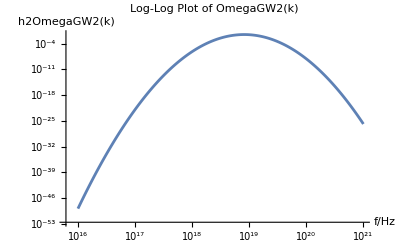

Constants and Functions.

```mathematica
MSPowerSolutions = Transpose[{frequencies, MSPowerSolutions1}]; cg = 0.4; OmegaR0 = 2.47/10^5; Ic[d_, s_] := -36*Pi*((s^2 + d^2 - 2)^2/(s^2 - d^2)^3)*UnitStep[s - 1]; Is[d_, s_] := -36*((s^2 + d^2 - 2)/(s^2 - d^2)^2)*(((s^2 + d^2 - 2)/(s^2 - d^2))*Log[(1 - d^2)/Abs[s^2 - 1]] + 2);
```

Interpolate the power spectrum so we have P as a function of k.

```mathematica
LogPInterpolation = Interpolation[Log10[MSPowerSolutions], InterpolationOrder -> 1]; P[k_] := 10^LogPInterpolation[Log10[k]]; kMin = Min[MSPowerSolutions[[All,1]]]; kMax = Max[MSPowerSolutions[[All,1]]];
```

Plot P[k] over the range of k values.

```mathematica
Expr = LogLogPlot[P[k], {k, kMin, kMax}, PlotRange -> All, AxesLabel -> {"k", "P(k)"}, PlotLabel -> "PowerSpectrumP(k)", GridLines -> Automatic];
```

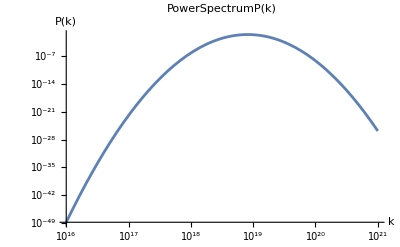

Calculate GW signature.

```mathematica
Integrand2[k_, d_, s_] := ((d^2 - 1/3)*((s^2 - 1/3)/(s^2 - d^2)))^2*P[k*Sqrt[3]*((s + d)/2)]*P[k*Sqrt[3]*((s - d)/2)]*(Is[d, s]^2 + Ic[d, s]^2); h2OmegaGW2[k_] := cg*(OmegaR0/36)*NIntegrate[Integrand2[k, d, s], {d, 0, 1/Sqrt[3]}, {s, 1/Sqrt[3], Infinity}, WorkingPrecision -> 40];
```

Local Adaptive can often taken a while to run, in which case Adaptive Monte Carlo is recommended for quick but reliable estimates.

Frequency region to plot GW signature in.

```mathematica
lowF = 10^(-2); highF = 10^6; conv = 1.546/10^15; k1 = 10^Range[Log10[lowF/conv], Log10[highF/conv], (Log10[highF/conv] - Log10[lowF/conv])/1000];
```

{6.46831×10^12,6.58856×10^12,6.71105×10^12,6.83582×10^12,6.96291×10^12,7.09236×10^12,7.22421×10^12,7.35852×10^12,7.49533×10^12,7.63467×10^12,7.77661×10^12,7.92119×10^12,8.06846×10^12,8.21846×10^12,8.37125×10^12,8.52689×10^12,8.68541×10^12,8.84689×10^12,9.01136×10^12,9.1789×10^12,9.34955×10^12,9.52337×10^12,9.70042×10^12,9.88076×10^12,1.00645×10^13,1.02516×10^13,1.04422×10^13,1.06363×10^13,1.0834×10^13,1.10355×10^13,1.12406×10^13,1.14496×10^13,1.16625×10^13,1.18793×10^13,1.21001×10^13,1.23251×10^13,1.25542×10^13,1.27876×10^13,1.30254×10^13,1.32675×10^13,1.35142×10^13,1.37655×10^13,1.40214×10^13,1.4282×10^13,1.45476×10^13,1.4818×10^13,1.50935×10^13,1.53741×10^13,1.566×10^13,1.59511×10^13,1.62476×10^13,1.65497×10^13,1.68574×10^13,1.71708×10^13,1.749×10^13,1.78152×10^13,1.81464×10^13,1.84838×10^13,1.88274×10^13,1.91774×10^13,1.9534×10^13,1.98971×10^13,2.0267×10^13,2.06438×10^13,2.10276×10^13,2.14186×10^13,2.18168×10^13,2.22224×10^13,2.26355×10^13,2.30563×10^13,2.3485×10^13,2.39216×10^13,2.43664×10^13,2.48194×10^13,2.52808×10^13,2.57508×10^13,2.62295×10^13,2.67172×10^13,2.72139×10^13,2.77198×10^13,2.82352×10^13,2.87601×10^13,2.92948×10^13,2.98394×10^13,3.03942×10^13,3.09593×10^13,3.15348×10^13,3.21211×10^13,3.27183×10^13,3.33266×10^13,3.39461×10^13,3.45773×10^13,3.52201×10^13,3.58749×10^13,3.65418×10^13,3.72212×10^13,3.79132×10^13,3.86181×10^13,3.9336×10^13,4.00673×10^13,4.08122×10^13,4.1571×10^13,4.23439×10^13,4.31311×10^13,4.3933×10^13,4.47497×10^13,4.55817×10^13,4.64291×10^13,4.72923×10^13,4.81715×10^13,4.90671×10^13,4.99793×10^13,5.09085×10^13,5.1855×10^13,5.2819×10^13,5.3801×10^13,5.48013×10^13,5.58201×10^13,5.68579×10^13,5.79149×10^13,5.89916×10^13,6.00884×10^13,6.12055×10^13,6.23434×10^13,6.35025×10^13,6.46831×10^13,6.58856×10^13,6.71105×10^13,6.83582×10^13,6.96291×10^13,7.09236×10^13,7.22421×10^13,7.35852×10^13,7.49533×10^13,7.63467×10^13,7.77661×10^13,7.92119×10^13,8.06846×10^13,8.21846×10^13,8.37125×10^13,8.52689×10^13,8.68541×10^13,8.84689×10^13,9.01136×10^13,9.1789×10^13,9.34955×10^13,9.52337×10^13,9.70042×10^13,9.88076×10^13,1.00645×10^14,1.02516×10^14,1.04422×10^14,1.06363×10^14,1.0834×10^14,1.10355×10^14,1.12406×10^14,1.14496×10^14,1.16625×10^14,1.18793×10^14,1.21001×10^14,1.23251×10^14,1.25542×10^14,1.27876×10^14,1.30254×10^14,1.32675×10^14,1.35142×10^14,1.37655×10^14,1.40214×10^14,1.4282×10^14,1.45476×10^14,1.4818×10^14,1.50935×10^14,1.53741×10^14,1.566×10^14,1.59511×10^14,1.62476×10^14,1.65497×10^14,1.68574×10^14,1.71708×10^14,1.749×10^14,1.78152×10^14,1.81464×10^14,1.84838×10^14,1.88274×10^14,1.91774×10^14,1.9534×10^14,1.98971×10^14,2.0267×10^14,2.06438×10^14,2.10276×10^14,2.14186×10^14,2.18168×10^14,2.22224×10^14,2.26355×10^14,2.30563×10^14,2.3485×10^14,2.39216×10^14,2.43664×10^14,2.48194×10^14,2.52808×10^14,2.57508×10^14,2.62295×10^14,2.67172×10^14,2.72139×10^14,2.77198×10^14,2.82352×10^14,2.87601×10^14,2.92948×10^14,2.98394×10^14,3.03942×10^14,3.09593×10^14,3.15348×10^14,3.21211×10^14,3.27183×10^14,3.33266×10^14,3.39461×10^14,3.45773×10^14,3.52201×10^14,3.58749×10^14,3.65418×10^14,3.72212×10^14,3.79132×10^14,3.86181×10^14,3.9336×10^14,4.00673×10^14,4.08122×10^14,4.1571×10^14,4.23439×10^14,4.31311×10^14,4.3933×10^14,4.47497×10^14,4.55817×10^14,4.64291×10^14,4.72923×10^14,4.81715×10^14,4.90671×10^14,4.99793×10^14,5.09085×10^14,5.1855×10^14,5.2819×10^14,5.3801×10^14,5.48013×10^14,5.58201×10^14,5.68579×10^14,5.79149×10^14,5.89916×10^14,6.00884×10^14,6.12055×10^14,6.23434×10^14,6.35025×10^14,6.46831×10^14,6.58856×10^14,6.71105×10^14,6.83582×10^14,6.96291×10^14,7.09236×10^14,7.22421×10^14,7.35852×10^14,7.49533×10^14,7.63467×10^14,7.77661×10^14,7.92119×10^14,8.06846×10^14,8.21846×10^14,8.37125×10^14,8.52689×10^14,8.68541×10^14,8.84689×10^14,9.01136×10^14,9.1789×10^14,9.34955×10^14,9.52337×10^14,9.70042×10^14,9.88076×10^14,1.00645×10^15,1.02516×10^15,1.04422×10^15,1.06363×10^15,1.0834×10^15,1.10355×10^15,1.12406×10^15,1.14496×10^15,1.16625×10^15,1.18793×10^15,1.21001×10^15,1.23251×10^15,1.25542×10^15,1.27876×10^15,1.30254×10^15,1.32675×10^15,1.35142×10^15,1.37655×10^15,1.40214×10^15,1.4282×10^15,1.45476×10^15,1.4818×10^15,1.50935×10^15,1.53741×10^15,1.566×10^15,1.59511×10^15,1.62476×10^15,1.65497×10^15,1.68574×10^15,1.71708×10^15,1.749×10^15,1.78152×10^15,1.81464×10^15,1.84838×10^15,1.88274×10^15,1.91774×10^15,1.9534×10^15,1.98971×10^15,2.0267×10^15,2.06438×10^15,2.10276×10^15,2.14186×10^15,2.18168×10^15,2.22224×10^15,2.26355×10^15,2.30563×10^15,2.3485×10^15,2.39216×10^15,2.43664×10^15,2.48194×10^15,2.52808×10^15,2.57508×10^15,2.62295×10^15,2.67172×10^15,2.72139×10^15,2.77198×10^15,2.82352×10^15,2.87601×10^15,2.92948×10^15,2.98394×10^15,3.03942×10^15,3.09593×10^15,3.15348×10^15,3.21211×10^15,3.27183×10^15,3.33266×10^15,3.39461×10^15,3.45773×10^15,3.52201×10^15,3.58749×10^15,3.65418×10^15,3.72212×10^15,3.79132×10^15,3.86181×10^15,3.9336×10^15,4.00673×10^15,4.08122×10^15,4.1571×10^15,4.23439×10^15,4.31311×10^15,4.3933×10^15,4.47497×10^15,4.55817×10^15,4.64291×10^15,4.72923×10^15,4.81715×10^15,4.90671×10^15,4.99793×10^15,5.09085×10^15,5.1855×10^15,5.2819×10^15,5.3801×10^15,5.48013×10^15,5.58201×10^15,5.68579×10^15,5.79149×10^15,5.89916×10^15,6.00884×10^15,6.12055×10^15,6.23434×10^15,6.35025×10^15,6.46831×10^15,6.58856×10^15,6.71105×10^15,6.83582×10^15,6.96291×10^15,7.09236×10^15,7.22421×10^15,7.35852×10^15,7.49533×10^15,7.63467×10^15,7.77661×10^15,7.92119×10^15,8.06846×10^15,8.21846×10^15,8.37125×10^15,8.52689×10^15,8.68541×10^15,8.84689×10^15,9.01136×10^15,9.1789×10^15,9.34955×10^15,9.52337×10^15,9.70042×10^15,9.88076×10^15,1.00645×10^16,1.02516×10^16,1.04422×10^16,1.06363×10^16,1.0834×10^16,1.10355×10^16,1.12406×10^16,1.14496×10^16,1.16625×10^16,1.18793×10^16,1.21001×10^16,1.23251×10^16,1.25542×10^16,1.27876×10^16,1.30254×10^16,1.32675×10^16,1.35142×10^16,1.37655×10^16,1.40214×10^16,1.4282×10^16,1.45476×10^16,1.4818×10^16,1.50935×10^16,1.53741×10^16,1.566×10^16,1.59511×10^16,1.62476×10^16,1.65497×10^16,1.68574×10^16,1.71708×10^16,1.749×10^16,1.78152×10^16,1.81464×10^16,1.84838×10^16,1.88274×10^16,1.91774×10^16,1.9534×10^16,1.98971×10^16,2.0267×10^16,2.06438×10^16,2.10276×10^16,2.14186×10^16,2.18168×10^16,2.22224×10^16,2.26355×10^16,2.30563×10^16,2.3485×10^16,2.39216×10^16,2.43664×10^16,2.48194×10^16,2.52808×10^16,2.57508×10^16,2.62295×10^16,2.67172×10^16,2.72139×10^16,2.77198×10^16,2.82352×10^16,2.87601×10^16,2.92948×10^16,2.98394×10^16,3.03942×10^16,3.09593×10^16,3.15348×10^16,3.21211×10^16,3.27183×10^16,3.33266×10^16,3.39461×10^16,3.45773×10^16,3.52201×10^16,3.58749×10^16,3.65418×10^16,3.72212×10^16,3.79132×10^16,3.86181×10^16,3.9336×10^16,4.00673×10^16,4.08122×10^16,4.1571×10^16,4.23439×10^16,4.31311×10^16,4.3933×10^16,4.47497×10^16,4.55817×10^16,4.64291×10^16,4.72923×10^16,4.81715×10^16,4.90671×10^16,4.99793×10^16,5.09085×10^16,5.1855×10^16,5.2819×10^16,5.3801×10^16,5.48013×10^16,5.58201×10^16,5.68579×10^16,5.79149×10^16,5.89916×10^16,6.00884×10^16,6.12055×10^16,6.23434×10^16,6.35025×10^16,6.46831×10^16,6.58856×10^16,6.71105×10^16,6.83582×10^16,6.96291×10^16,7.09236×10^16,7.22421×10^16,7.35852×10^16,7.49533×10^16,7.63467×10^16,7.77661×10^16,7.92119×10^16,8.06846×10^16,8.21846×10^16,8.37125×10^16,8.52689×10^16,8.68541×10^16,8.84689×10^16,9.01136×10^16,9.1789×10^16,9.34955×10^16,9.52337×10^16,9.70042×10^16,9.88076×10^16,1.00645×10^17,1.02516×10^17,1.04422×10^17,1.06363×10^17,1.0834×10^17,1.10355×10^17,1.12406×10^17,1.14496×10^17,1.16625×10^17,1.18793×10^17,1.21001×10^17,1.23251×10^17,1.25542×10^17,1.27876×10^17,1.30254×10^17,1.32675×10^17,1.35142×10^17,1.37655×10^17,1.40214×10^17,1.4282×10^17,1.45476×10^17,1.4818×10^17,1.50935×10^17,1.53741×10^17,1.566×10^17,1.59511×10^17,1.62476×10^17,1.65497×10^17,1.68574×10^17,1.71708×10^17,1.749×10^17,1.78152×10^17,1.81464×10^17,1.84838×10^17,1.88274×10^17,1.91774×10^17,1.9534×10^17,1.98971×10^17,2.0267×10^17,2.06438×10^17,2.10276×10^17,2.14186×10^17,2.18168×10^17,2.22224×10^17,2.26355×10^17,2.30563×10^17,2.3485×10^17,2.39216×10^17,2.43664×10^17,2.48194×10^17,2.52808×10^17,2.57508×10^17,2.62295×10^17,2.67172×10^17,2.72139×10^17,2.77198×10^17,2.82352×10^17,2.87601×10^17,2.92948×10^17,2.98394×10^17,3.03942×10^17,3.09593×10^17,3.15348×10^17,3.21211×10^17,3.27183×10^17,3.33266×10^17,3.39461×10^17,3.45773×10^17,3.52201×10^17,3.58749×10^17,3.65418×10^17,3.72212×10^17,3.79132×10^17,3.86181×10^17,3.9336×10^17,4.00673×10^17,4.08122×10^17,4.1571×10^17,4.23439×10^17,4.31311×10^17,4.3933×10^17,4.47497×10^17,4.55817×10^17,4.64291×10^17,4.72923×10^17,4.81715×10^17,4.90671×10^17,4.99793×10^17,5.09085×10^17,5.1855×10^17,5.2819×10^17,5.3801×10^17,5.48013×10^17,5.58201×10^17,5.68579×10^17,5.79149×10^17,5.89916×10^17,6.00884×10^17,6.12055×10^17,6.23434×10^17,6.35025×10^17,6.46831×10^17,6.58856×10^17,6.71105×10^17,6.83582×10^17,6.96291×10^17,7.09236×10^17,7.22421×10^17,7.35852×10^17,7.49533×10^17,7.63467×10^17,7.77661×10^17,7.92119×10^17,8.06846×10^17,8.21846×10^17,8.37125×10^17,8.52689×10^17,8.68541×10^17,8.84689×10^17,9.01136×10^17,9.1789×10^17,9.34955×10^17,9.52337×10^17,9.70042×10^17,9.88076×10^17,1.00645×10^18,1.02516×10^18,1.04422×10^18,1.06363×10^18,1.0834×10^18,1.10355×10^18,1.12406×10^18,1.14496×10^18,1.16625×10^18,1.18793×10^18,1.21001×10^18,1.23251×10^18,1.25542×10^18,1.27876×10^18,1.30254×10^18,1.32675×10^18,1.35142×10^18,1.37655×10^18,1.40214×10^18,1.4282×10^18,1.45476×10^18,1.4818×10^18,1.50935×10^18,1.53741×10^18,1.566×10^18,1.59511×10^18,1.62476×10^18,1.65497×10^18,1.68574×10^18,1.71708×10^18,1.749×10^18,1.78152×10^18,1.81464×10^18,1.84838×10^18,1.88274×10^18,1.91774×10^18,1.9534×10^18,1.98971×10^18,2.0267×10^18,2.06438×10^18,2.10276×10^18,2.14186×10^18,2.18168×10^18,2.22224×10^18,2.26355×10^18,2.30563×10^18,2.3485×10^18,2.39216×10^18,2.43664×10^18,2.48194×10^18,2.52808×10^18,2.57508×10^18,2.62295×10^18,2.67172×10^18,2.72139×10^18,2.77198×10^18,2.82352×10^18,2.87601×10^18,2.92948×10^18,2.98394×10^18,3.03942×10^18,3.09593×10^18,3.15348×10^18,3.21211×10^18,3.27183×10^18,3.33266×10^18,3.39461×10^18,3.45773×10^18,3.52201×10^18,3.58749×10^18,3.65418×10^18,3.72212×10^18,3.79132×10^18,3.86181×10^18,3.9336×10^18,4.00673×10^18,4.08122×10^18,4.1571×10^18,4.23439×10^18,4.31311×10^18,4.3933×10^18,4.47497×10^18,4.55817×10^18,4.64291×10^18,4.72923×10^18,4.81715×10^18,4.90671×10^18,4.99793×10^18,5.09085×10^18,5.1855×10^18,5.2819×10^18,5.3801×10^18,5.48013×10^18,5.58201×10^18,5.68579×10^18,5.79149×10^18,5.89916×10^18,6.00884×10^18,6.12055×10^18,6.23434×10^18,6.35025×10^18,6.46831×10^18,6.58856×10^18,6.71105×10^18,6.83582×10^18,6.96291×10^18,7.09236×10^18,7.22421×10^18,7.35852×10^18,7.49533×10^18,7.63467×10^18,7.77661×10^18,7.92119×10^18,8.06846×10^18,8.21846×10^18,8.37125×10^18,8.52689×10^18,8.68541×10^18,8.84689×10^18,9.01136×10^18,9.1789×10^18,9.34955×10^18,9.52337×10^18,9.70042×10^18,9.88076×10^18,1.00645×10^19,1.02516×10^19,1.04422×10^19,1.06363×10^19,1.0834×10^19,1.10355×10^19,1.12406×10^19,1.14496×10^19,1.16625×10^19,1.18793×10^19,1.21001×10^19,1.23251×10^19,1.25542×10^19,1.27876×10^19,1.30254×10^19,1.32675×10^19,1.35142×10^19,1.37655×10^19,1.40214×10^19,1.4282×10^19,1.45476×10^19,1.4818×10^19,1.50935×10^19,1.53741×10^19,1.566×10^19,1.59511×10^19,1.62476×10^19,1.65497×10^19,1.68574×10^19,1.71708×10^19,1.749×10^19,1.78152×10^19,1.81464×10^19,1.84838×10^19,1.88274×10^19,1.91774×10^19,1.9534×10^19,1.98971×10^19,2.0267×10^19,2.06438×10^19,2.10276×10^19,2.14186×10^19,2.18168×10^19,2.22224×10^19,2.26355×10^19,2.30563×10^19,2.3485×10^19,2.39216×10^19,2.43664×10^19,2.48194×10^19,2.52808×10^19,2.57508×10^19,2.62295×10^19,2.67172×10^19,2.72139×10^19,2.77198×10^19,2.82352×10^19,2.87601×10^19,2.92948×10^19,2.98394×10^19,3.03942×10^19,3.09593×10^19,3.15348×10^19,3.21211×10^19,3.27183×10^19,3.33266×10^19,3.39461×10^19,3.45773×10^19,3.52201×10^19,3.58749×10^19,3.65418×10^19,3.72212×10^19,3.79132×10^19,3.86181×10^19,3.9336×10^19,4.00673×10^19,4.08122×10^19,4.1571×10^19,4.23439×10^19,4.31311×10^19,4.3933×10^19,4.47497×10^19,4.55817×10^19,4.64291×10^19,4.72923×10^19,4.81715×10^19,4.90671×10^19,4.99793×10^19,5.09085×10^19,5.1855×10^19,5.2819×10^19,5.3801×10^19,5.48013×10^19,5.58201×10^19,5.68579×10^19,5.79149×10^19,5.89916×10^19,6.00884×10^19,6.12055×10^19,6.23434×10^19,6.35025×10^19,6.46831×10^19,6.58856×10^19,6.71105×10^19,6.83582×10^19,6.96291×10^19,7.09236×10^19,7.22421×10^19,7.35852×10^19,7.49533×10^19,7.63467×10^19,7.77661×10^19,7.92119×10^19,8.06846×10^19,8.21846×10^19,8.37125×10^19,8.52689×10^19,8.68541×10^19,8.84689×10^19,9.01136×10^19,9.1789×10^19,9.34955×10^19,9.52337×10^19,9.70042×10^19,9.88076×10^19,1.00645×10^20,1.02516×10^20,1.04422×10^20,1.06363×10^20,1.0834×10^20,1.10355×10^20,1.12406×10^20,1.14496×10^20,1.16625×10^20,1.18793×10^20,1.21001×10^20,1.23251×10^20,1.25542×10^20,1.27876×10^20,1.30254×10^20,1.32675×10^20,1.35142×10^20,1.37655×10^20,1.40214×10^20,1.4282×10^20,1.45476×10^20,1.4818×10^20,1.50935×10^20,1.53741×10^20,1.566×10^20,1.59511×10^20,1.62476×10^20,1.65497×10^20,1.68574×10^20,1.71708×10^20,1.749×10^20,1.78152×10^20,1.81464×10^20,1.84838×10^20,1.88274×10^20,1.91774×10^20,1.9534×10^20,1.98971×10^20,2.0267×10^20,2.06438×10^20,2.10276×10^20,2.14186×10^20,2.18168×10^20,2.22224×10^20,2.26355×10^20,2.30563×10^20,2.3485×10^20,2.39216×10^20,2.43664×10^20,2.48194×10^20,2.52808×10^20,2.57508×10^20,2.62295×10^20,2.67172×10^20,2.72139×10^20,2.77198×10^20,2.82352×10^20,2.87601×10^20,2.92948×10^20,2.98394×10^20,3.03942×10^20,3.09593×10^20,3.15348×10^20,3.21211×10^20,3.27183×10^20,3.33266×10^20,3.39461×10^20,3.45773×10^20,3.52201×10^20,3.58749×10^20,3.65418×10^20,3.72212×10^20,3.79132×10^20,3.86181×10^20,3.9336×10^20,4.00673×10^20,4.08122×10^20,4.1571×10^20,4.23439×10^20,4.31311×10^20,4.3933×10^20,4.47497×10^20,4.55817×10^20,4.64291×10^20,4.72923×10^20,4.81715×10^20,4.90671×10^20,4.99793×10^20,5.09085×10^20,5.1855×10^20,5.2819×10^20,5.3801×10^20,5.48013×10^20,5.58201×10^20,5.68579×10^20,5.79149×10^20,5.89916×10^20,6.00884×10^20,6.12055×10^20,6.23434×10^20,6.35025×10^20,6.46831×10^20}

Calculate the GW signature for the given frequency range.

```mathematica
Get[FileNameJoin[{Directory[], StringJoin["1e8g_GaussianFitted", "_GW.mx"]}]];
```

Plot.

```mathematica
Expr = ListLogLogPlot[Transpose[{conv*k1, h2OmegaGW2Sol}], Joined -> True, AxesLabel -> {"f/Hz", "h2OmegaGW2(k)"}, PlotLabel -> "Log-LogPlotofOmegaGW2(k)", PlotRange -> {Automatic, Automatic}]; Export[StringJoin["1e8g_GaussianFitted", "_GW.csv"], Transpose[{conv*k1, h2OmegaGW2Sol}], "CSV"];
```

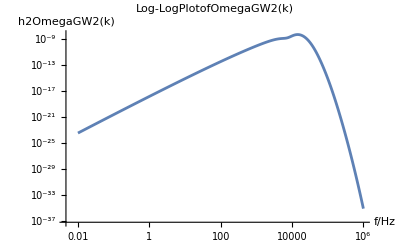

```mathematica
"First we import the data from the power spectrum file."
```

```mathematica
filePath = StringJoin["1e8g_GaussianFitted_d_1", "_PowerSpectrum.txt"]; data = Import[filePath, "Data"];
```

If you want to extract the individual columns for further processing.

```mathematica
frequencies = data[[All,1]]; MSPowerSolutions1 = data[[All,2]];
```

For example,you can create a plot.

```mathematica
Expr = ListLogLogPlot[Transpose[{frequencies, MSPowerSolutions1}], Joined -> True, AxesLabel -> {"f/Hz", "h2OmegaGW2(k)"}, PlotLabel -> "Log-Log Plot of OmegaGW2(k)", PlotRange -> {Automatic, Automatic}];
```

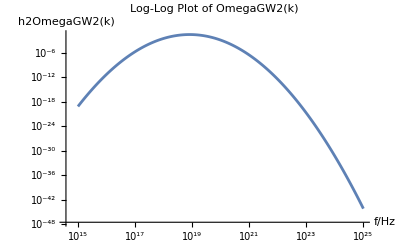

Constants and Functions.

```mathematica
MSPowerSolutions = Transpose[{frequencies, MSPowerSolutions1}]; cg = 0.4; OmegaR0 = 2.47/10^5; Ic[d_, s_] := -36*Pi*((s^2 + d^2 - 2)^2/(s^2 - d^2)^3)*UnitStep[s - 1]; Is[d_, s_] := -36*((s^2 + d^2 - 2)/(s^2 - d^2)^2)*(((s^2 + d^2 - 2)/(s^2 - d^2))*Log[(1 - d^2)/Abs[s^2 - 1]] + 2);
```

Interpolate the power spectrum so we have P as a function of k.

```mathematica
LogPInterpolation = Interpolation[Log10[MSPowerSolutions], InterpolationOrder -> 1]; P[k_] := 10^LogPInterpolation[Log10[k]]; kMin = Min[MSPowerSolutions[[All,1]]]; kMax = Max[MSPowerSolutions[[All,1]]];
```

Plot P[k] over the range of k values.

```mathematica
Expr = LogLogPlot[P[k], {k, kMin, kMax}, PlotRange -> All, AxesLabel -> {"k", "P(k)"}, PlotLabel -> "PowerSpectrumP(k)", GridLines -> Automatic];
```

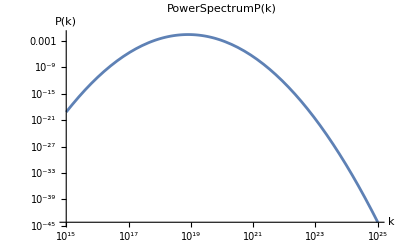

Calculate GW signature.

```mathematica
Integrand2[k_, d_, s_] := ((d^2 - 1/3)*((s^2 - 1/3)/(s^2 - d^2)))^2*P[k*Sqrt[3]*((s + d)/2)]*P[k*Sqrt[3]*((s - d)/2)]*(Is[d, s]^2 + Ic[d, s]^2); h2OmegaGW2[k_] := cg*(OmegaR0/36)*NIntegrate[Integrand2[k, d, s], {d, 0, 1/Sqrt[3]}, {s, 1/Sqrt[3], Infinity}, WorkingPrecision -> 40];
```

Local Adaptive can often taken a while to run, in which case Adaptive Monte Carlo is recommended for quick but reliable estimates.

Frequency region to plot GW signature in.

```mathematica
lowF = 10^(-2); highF = 10^6; conv = 1.546/10^15; k1 = 10^Range[Log10[lowF/conv], Log10[highF/conv], (Log10[highF/conv] - Log10[lowF/conv])/1000];
```

{6.46831×10^12,6.58856×10^12,6.71105×10^12,6.83582×10^12,6.96291×10^12,7.09236×10^12,7.22421×10^12,7.35852×10^12,7.49533×10^12,7.63467×10^12,7.77661×10^12,7.92119×10^12,8.06846×10^12,8.21846×10^12,8.37125×10^12,8.52689×10^12,8.68541×10^12,8.84689×10^12,9.01136×10^12,9.1789×10^12,9.34955×10^12,9.52337×10^12,9.70042×10^12,9.88076×10^12,1.00645×10^13,1.02516×10^13,1.04422×10^13,1.06363×10^13,1.0834×10^13,1.10355×10^13,1.12406×10^13,1.14496×10^13,1.16625×10^13,1.18793×10^13,1.21001×10^13,1.23251×10^13,1.25542×10^13,1.27876×10^13,1.30254×10^13,1.32675×10^13,1.35142×10^13,1.37655×10^13,1.40214×10^13,1.4282×10^13,1.45476×10^13,1.4818×10^13,1.50935×10^13,1.53741×10^13,1.566×10^13,1.59511×10^13,1.62476×10^13,1.65497×10^13,1.68574×10^13,1.71708×10^13,1.749×10^13,1.78152×10^13,1.81464×10^13,1.84838×10^13,1.88274×10^13,1.91774×10^13,1.9534×10^13,1.98971×10^13,2.0267×10^13,2.06438×10^13,2.10276×10^13,2.14186×10^13,2.18168×10^13,2.22224×10^13,2.26355×10^13,2.30563×10^13,2.3485×10^13,2.39216×10^13,2.43664×10^13,2.48194×10^13,2.52808×10^13,2.57508×10^13,2.62295×10^13,2.67172×10^13,2.72139×10^13,2.77198×10^13,2.82352×10^13,2.87601×10^13,2.92948×10^13,2.98394×10^13,3.03942×10^13,3.09593×10^13,3.15348×10^13,3.21211×10^13,3.27183×10^13,3.33266×10^13,3.39461×10^13,3.45773×10^13,3.52201×10^13,3.58749×10^13,3.65418×10^13,3.72212×10^13,3.79132×10^13,3.86181×10^13,3.9336×10^13,4.00673×10^13,4.08122×10^13,4.1571×10^13,4.23439×10^13,4.31311×10^13,4.3933×10^13,4.47497×10^13,4.55817×10^13,4.64291×10^13,4.72923×10^13,4.81715×10^13,4.90671×10^13,4.99793×10^13,5.09085×10^13,5.1855×10^13,5.2819×10^13,5.3801×10^13,5.48013×10^13,5.58201×10^13,5.68579×10^13,5.79149×10^13,5.89916×10^13,6.00884×10^13,6.12055×10^13,6.23434×10^13,6.35025×10^13,6.46831×10^13,6.58856×10^13,6.71105×10^13,6.83582×10^13,6.96291×10^13,7.09236×10^13,7.22421×10^13,7.35852×10^13,7.49533×10^13,7.63467×10^13,7.77661×10^13,7.92119×10^13,8.06846×10^13,8.21846×10^13,8.37125×10^13,8.52689×10^13,8.68541×10^13,8.84689×10^13,9.01136×10^13,9.1789×10^13,9.34955×10^13,9.52337×10^13,9.70042×10^13,9.88076×10^13,1.00645×10^14,1.02516×10^14,1.04422×10^14,1.06363×10^14,1.0834×10^14,1.10355×10^14,1.12406×10^14,1.14496×10^14,1.16625×10^14,1.18793×10^14,1.21001×10^14,1.23251×10^14,1.25542×10^14,1.27876×10^14,1.30254×10^14,1.32675×10^14,1.35142×10^14,1.37655×10^14,1.40214×10^14,1.4282×10^14,1.45476×10^14,1.4818×10^14,1.50935×10^14,1.53741×10^14,1.566×10^14,1.59511×10^14,1.62476×10^14,1.65497×10^14,1.68574×10^14,1.71708×10^14,1.749×10^14,1.78152×10^14,1.81464×10^14,1.84838×10^14,1.88274×10^14,1.91774×10^14,1.9534×10^14,1.98971×10^14,2.0267×10^14,2.06438×10^14,2.10276×10^14,2.14186×10^14,2.18168×10^14,2.22224×10^14,2.26355×10^14,2.30563×10^14,2.3485×10^14,2.39216×10^14,2.43664×10^14,2.48194×10^14,2.52808×10^14,2.57508×10^14,2.62295×10^14,2.67172×10^14,2.72139×10^14,2.77198×10^14,2.82352×10^14,2.87601×10^14,2.92948×10^14,2.98394×10^14,3.03942×10^14,3.09593×10^14,3.15348×10^14,3.21211×10^14,3.27183×10^14,3.33266×10^14,3.39461×10^14,3.45773×10^14,3.52201×10^14,3.58749×10^14,3.65418×10^14,3.72212×10^14,3.79132×10^14,3.86181×10^14,3.9336×10^14,4.00673×10^14,4.08122×10^14,4.1571×10^14,4.23439×10^14,4.31311×10^14,4.3933×10^14,4.47497×10^14,4.55817×10^14,4.64291×10^14,4.72923×10^14,4.81715×10^14,4.90671×10^14,4.99793×10^14,5.09085×10^14,5.1855×10^14,5.2819×10^14,5.3801×10^14,5.48013×10^14,5.58201×10^14,5.68579×10^14,5.79149×10^14,5.89916×10^14,6.00884×10^14,6.12055×10^14,6.23434×10^14,6.35025×10^14,6.46831×10^14,6.58856×10^14,6.71105×10^14,6.83582×10^14,6.96291×10^14,7.09236×10^14,7.22421×10^14,7.35852×10^14,7.49533×10^14,7.63467×10^14,7.77661×10^14,7.92119×10^14,8.06846×10^14,8.21846×10^14,8.37125×10^14,8.52689×10^14,8.68541×10^14,8.84689×10^14,9.01136×10^14,9.1789×10^14,9.34955×10^14,9.52337×10^14,9.70042×10^14,9.88076×10^14,1.00645×10^15,1.02516×10^15,1.04422×10^15,1.06363×10^15,1.0834×10^15,1.10355×10^15,1.12406×10^15,1.14496×10^15,1.16625×10^15,1.18793×10^15,1.21001×10^15,1.23251×10^15,1.25542×10^15,1.27876×10^15,1.30254×10^15,1.32675×10^15,1.35142×10^15,1.37655×10^15,1.40214×10^15,1.4282×10^15,1.45476×10^15,1.4818×10^15,1.50935×10^15,1.53741×10^15,1.566×10^15,1.59511×10^15,1.62476×10^15,1.65497×10^15,1.68574×10^15,1.71708×10^15,1.749×10^15,1.78152×10^15,1.81464×10^15,1.84838×10^15,1.88274×10^15,1.91774×10^15,1.9534×10^15,1.98971×10^15,2.0267×10^15,2.06438×10^15,2.10276×10^15,2.14186×10^15,2.18168×10^15,2.22224×10^15,2.26355×10^15,2.30563×10^15,2.3485×10^15,2.39216×10^15,2.43664×10^15,2.48194×10^15,2.52808×10^15,2.57508×10^15,2.62295×10^15,2.67172×10^15,2.72139×10^15,2.77198×10^15,2.82352×10^15,2.87601×10^15,2.92948×10^15,2.98394×10^15,3.03942×10^15,3.09593×10^15,3.15348×10^15,3.21211×10^15,3.27183×10^15,3.33266×10^15,3.39461×10^15,3.45773×10^15,3.52201×10^15,3.58749×10^15,3.65418×10^15,3.72212×10^15,3.79132×10^15,3.86181×10^15,3.9336×10^15,4.00673×10^15,4.08122×10^15,4.1571×10^15,4.23439×10^15,4.31311×10^15,4.3933×10^15,4.47497×10^15,4.55817×10^15,4.64291×10^15,4.72923×10^15,4.81715×10^15,4.90671×10^15,4.99793×10^15,5.09085×10^15,5.1855×10^15,5.2819×10^15,5.3801×10^15,5.48013×10^15,5.58201×10^15,5.68579×10^15,5.79149×10^15,5.89916×10^15,6.00884×10^15,6.12055×10^15,6.23434×10^15,6.35025×10^15,6.46831×10^15,6.58856×10^15,6.71105×10^15,6.83582×10^15,6.96291×10^15,7.09236×10^15,7.22421×10^15,7.35852×10^15,7.49533×10^15,7.63467×10^15,7.77661×10^15,7.92119×10^15,8.06846×10^15,8.21846×10^15,8.37125×10^15,8.52689×10^15,8.68541×10^15,8.84689×10^15,9.01136×10^15,9.1789×10^15,9.34955×10^15,9.52337×10^15,9.70042×10^15,9.88076×10^15,1.00645×10^16,1.02516×10^16,1.04422×10^16,1.06363×10^16,1.0834×10^16,1.10355×10^16,1.12406×10^16,1.14496×10^16,1.16625×10^16,1.18793×10^16,1.21001×10^16,1.23251×10^16,1.25542×10^16,1.27876×10^16,1.30254×10^16,1.32675×10^16,1.35142×10^16,1.37655×10^16,1.40214×10^16,1.4282×10^16,1.45476×10^16,1.4818×10^16,1.50935×10^16,1.53741×10^16,1.566×10^16,1.59511×10^16,1.62476×10^16,1.65497×10^16,1.68574×10^16,1.71708×10^16,1.749×10^16,1.78152×10^16,1.81464×10^16,1.84838×10^16,1.88274×10^16,1.91774×10^16,1.9534×10^16,1.98971×10^16,2.0267×10^16,2.06438×10^16,2.10276×10^16,2.14186×10^16,2.18168×10^16,2.22224×10^16,2.26355×10^16,2.30563×10^16,2.3485×10^16,2.39216×10^16,2.43664×10^16,2.48194×10^16,2.52808×10^16,2.57508×10^16,2.62295×10^16,2.67172×10^16,2.72139×10^16,2.77198×10^16,2.82352×10^16,2.87601×10^16,2.92948×10^16,2.98394×10^16,3.03942×10^16,3.09593×10^16,3.15348×10^16,3.21211×10^16,3.27183×10^16,3.33266×10^16,3.39461×10^16,3.45773×10^16,3.52201×10^16,3.58749×10^16,3.65418×10^16,3.72212×10^16,3.79132×10^16,3.86181×10^16,3.9336×10^16,4.00673×10^16,4.08122×10^16,4.1571×10^16,4.23439×10^16,4.31311×10^16,4.3933×10^16,4.47497×10^16,4.55817×10^16,4.64291×10^16,4.72923×10^16,4.81715×10^16,4.90671×10^16,4.99793×10^16,5.09085×10^16,5.1855×10^16,5.2819×10^16,5.3801×10^16,5.48013×10^16,5.58201×10^16,5.68579×10^16,5.79149×10^16,5.89916×10^16,6.00884×10^16,6.12055×10^16,6.23434×10^16,6.35025×10^16,6.46831×10^16,6.58856×10^16,6.71105×10^16,6.83582×10^16,6.96291×10^16,7.09236×10^16,7.22421×10^16,7.35852×10^16,7.49533×10^16,7.63467×10^16,7.77661×10^16,7.92119×10^16,8.06846×10^16,8.21846×10^16,8.37125×10^16,8.52689×10^16,8.68541×10^16,8.84689×10^16,9.01136×10^16,9.1789×10^16,9.34955×10^16,9.52337×10^16,9.70042×10^16,9.88076×10^16,1.00645×10^17,1.02516×10^17,1.04422×10^17,1.06363×10^17,1.0834×10^17,1.10355×10^17,1.12406×10^17,1.14496×10^17,1.16625×10^17,1.18793×10^17,1.21001×10^17,1.23251×10^17,1.25542×10^17,1.27876×10^17,1.30254×10^17,1.32675×10^17,1.35142×10^17,1.37655×10^17,1.40214×10^17,1.4282×10^17,1.45476×10^17,1.4818×10^17,1.50935×10^17,1.53741×10^17,1.566×10^17,1.59511×10^17,1.62476×10^17,1.65497×10^17,1.68574×10^17,1.71708×10^17,1.749×10^17,1.78152×10^17,1.81464×10^17,1.84838×10^17,1.88274×10^17,1.91774×10^17,1.9534×10^17,1.98971×10^17,2.0267×10^17,2.06438×10^17,2.10276×10^17,2.14186×10^17,2.18168×10^17,2.22224×10^17,2.26355×10^17,2.30563×10^17,2.3485×10^17,2.39216×10^17,2.43664×10^17,2.48194×10^17,2.52808×10^17,2.57508×10^17,2.62295×10^17,2.67172×10^17,2.72139×10^17,2.77198×10^17,2.82352×10^17,2.87601×10^17,2.92948×10^17,2.98394×10^17,3.03942×10^17,3.09593×10^17,3.15348×10^17,3.21211×10^17,3.27183×10^17,3.33266×10^17,3.39461×10^17,3.45773×10^17,3.52201×10^17,3.58749×10^17,3.65418×10^17,3.72212×10^17,3.79132×10^17,3.86181×10^17,3.9336×10^17,4.00673×10^17,4.08122×10^17,4.1571×10^17,4.23439×10^17,4.31311×10^17,4.3933×10^17,4.47497×10^17,4.55817×10^17,4.64291×10^17,4.72923×10^17,4.81715×10^17,4.90671×10^17,4.99793×10^17,5.09085×10^17,5.1855×10^17,5.2819×10^17,5.3801×10^17,5.48013×10^17,5.58201×10^17,5.68579×10^17,5.79149×10^17,5.89916×10^17,6.00884×10^17,6.12055×10^17,6.23434×10^17,6.35025×10^17,6.46831×10^17,6.58856×10^17,6.71105×10^17,6.83582×10^17,6.96291×10^17,7.09236×10^17,7.22421×10^17,7.35852×10^17,7.49533×10^17,7.63467×10^17,7.77661×10^17,7.92119×10^17,8.06846×10^17,8.21846×10^17,8.37125×10^17,8.52689×10^17,8.68541×10^17,8.84689×10^17,9.01136×10^17,9.1789×10^17,9.34955×10^17,9.52337×10^17,9.70042×10^17,9.88076×10^17,1.00645×10^18,1.02516×10^18,1.04422×10^18,1.06363×10^18,1.0834×10^18,1.10355×10^18,1.12406×10^18,1.14496×10^18,1.16625×10^18,1.18793×10^18,1.21001×10^18,1.23251×10^18,1.25542×10^18,1.27876×10^18,1.30254×10^18,1.32675×10^18,1.35142×10^18,1.37655×10^18,1.40214×10^18,1.4282×10^18,1.45476×10^18,1.4818×10^18,1.50935×10^18,1.53741×10^18,1.566×10^18,1.59511×10^18,1.62476×10^18,1.65497×10^18,1.68574×10^18,1.71708×10^18,1.749×10^18,1.78152×10^18,1.81464×10^18,1.84838×10^18,1.88274×10^18,1.91774×10^18,1.9534×10^18,1.98971×10^18,2.0267×10^18,2.06438×10^18,2.10276×10^18,2.14186×10^18,2.18168×10^18,2.22224×10^18,2.26355×10^18,2.30563×10^18,2.3485×10^18,2.39216×10^18,2.43664×10^18,2.48194×10^18,2.52808×10^18,2.57508×10^18,2.62295×10^18,2.67172×10^18,2.72139×10^18,2.77198×10^18,2.82352×10^18,2.87601×10^18,2.92948×10^18,2.98394×10^18,3.03942×10^18,3.09593×10^18,3.15348×10^18,3.21211×10^18,3.27183×10^18,3.33266×10^18,3.39461×10^18,3.45773×10^18,3.52201×10^18,3.58749×10^18,3.65418×10^18,3.72212×10^18,3.79132×10^18,3.86181×10^18,3.9336×10^18,4.00673×10^18,4.08122×10^18,4.1571×10^18,4.23439×10^18,4.31311×10^18,4.3933×10^18,4.47497×10^18,4.55817×10^18,4.64291×10^18,4.72923×10^18,4.81715×10^18,4.90671×10^18,4.99793×10^18,5.09085×10^18,5.1855×10^18,5.2819×10^18,5.3801×10^18,5.48013×10^18,5.58201×10^18,5.68579×10^18,5.79149×10^18,5.89916×10^18,6.00884×10^18,6.12055×10^18,6.23434×10^18,6.35025×10^18,6.46831×10^18,6.58856×10^18,6.71105×10^18,6.83582×10^18,6.96291×10^18,7.09236×10^18,7.22421×10^18,7.35852×10^18,7.49533×10^18,7.63467×10^18,7.77661×10^18,7.92119×10^18,8.06846×10^18,8.21846×10^18,8.37125×10^18,8.52689×10^18,8.68541×10^18,8.84689×10^18,9.01136×10^18,9.1789×10^18,9.34955×10^18,9.52337×10^18,9.70042×10^18,9.88076×10^18,1.00645×10^19,1.02516×10^19,1.04422×10^19,1.06363×10^19,1.0834×10^19,1.10355×10^19,1.12406×10^19,1.14496×10^19,1.16625×10^19,1.18793×10^19,1.21001×10^19,1.23251×10^19,1.25542×10^19,1.27876×10^19,1.30254×10^19,1.32675×10^19,1.35142×10^19,1.37655×10^19,1.40214×10^19,1.4282×10^19,1.45476×10^19,1.4818×10^19,1.50935×10^19,1.53741×10^19,1.566×10^19,1.59511×10^19,1.62476×10^19,1.65497×10^19,1.68574×10^19,1.71708×10^19,1.749×10^19,1.78152×10^19,1.81464×10^19,1.84838×10^19,1.88274×10^19,1.91774×10^19,1.9534×10^19,1.98971×10^19,2.0267×10^19,2.06438×10^19,2.10276×10^19,2.14186×10^19,2.18168×10^19,2.22224×10^19,2.26355×10^19,2.30563×10^19,2.3485×10^19,2.39216×10^19,2.43664×10^19,2.48194×10^19,2.52808×10^19,2.57508×10^19,2.62295×10^19,2.67172×10^19,2.72139×10^19,2.77198×10^19,2.82352×10^19,2.87601×10^19,2.92948×10^19,2.98394×10^19,3.03942×10^19,3.09593×10^19,3.15348×10^19,3.21211×10^19,3.27183×10^19,3.33266×10^19,3.39461×10^19,3.45773×10^19,3.52201×10^19,3.58749×10^19,3.65418×10^19,3.72212×10^19,3.79132×10^19,3.86181×10^19,3.9336×10^19,4.00673×10^19,4.08122×10^19,4.1571×10^19,4.23439×10^19,4.31311×10^19,4.3933×10^19,4.47497×10^19,4.55817×10^19,4.64291×10^19,4.72923×10^19,4.81715×10^19,4.90671×10^19,4.99793×10^19,5.09085×10^19,5.1855×10^19,5.2819×10^19,5.3801×10^19,5.48013×10^19,5.58201×10^19,5.68579×10^19,5.79149×10^19,5.89916×10^19,6.00884×10^19,6.12055×10^19,6.23434×10^19,6.35025×10^19,6.46831×10^19,6.58856×10^19,6.71105×10^19,6.83582×10^19,6.96291×10^19,7.09236×10^19,7.22421×10^19,7.35852×10^19,7.49533×10^19,7.63467×10^19,7.77661×10^19,7.92119×10^19,8.06846×10^19,8.21846×10^19,8.37125×10^19,8.52689×10^19,8.68541×10^19,8.84689×10^19,9.01136×10^19,9.1789×10^19,9.34955×10^19,9.52337×10^19,9.70042×10^19,9.88076×10^19,1.00645×10^20,1.02516×10^20,1.04422×10^20,1.06363×10^20,1.0834×10^20,1.10355×10^20,1.12406×10^20,1.14496×10^20,1.16625×10^20,1.18793×10^20,1.21001×10^20,1.23251×10^20,1.25542×10^20,1.27876×10^20,1.30254×10^20,1.32675×10^20,1.35142×10^20,1.37655×10^20,1.40214×10^20,1.4282×10^20,1.45476×10^20,1.4818×10^20,1.50935×10^20,1.53741×10^20,1.566×10^20,1.59511×10^20,1.62476×10^20,1.65497×10^20,1.68574×10^20,1.71708×10^20,1.749×10^20,1.78152×10^20,1.81464×10^20,1.84838×10^20,1.88274×10^20,1.91774×10^20,1.9534×10^20,1.98971×10^20,2.0267×10^20,2.06438×10^20,2.10276×10^20,2.14186×10^20,2.18168×10^20,2.22224×10^20,2.26355×10^20,2.30563×10^20,2.3485×10^20,2.39216×10^20,2.43664×10^20,2.48194×10^20,2.52808×10^20,2.57508×10^20,2.62295×10^20,2.67172×10^20,2.72139×10^20,2.77198×10^20,2.82352×10^20,2.87601×10^20,2.92948×10^20,2.98394×10^20,3.03942×10^20,3.09593×10^20,3.15348×10^20,3.21211×10^20,3.27183×10^20,3.33266×10^20,3.39461×10^20,3.45773×10^20,3.52201×10^20,3.58749×10^20,3.65418×10^20,3.72212×10^20,3.79132×10^20,3.86181×10^20,3.9336×10^20,4.00673×10^20,4.08122×10^20,4.1571×10^20,4.23439×10^20,4.31311×10^20,4.3933×10^20,4.47497×10^20,4.55817×10^20,4.64291×10^20,4.72923×10^20,4.81715×10^20,4.90671×10^20,4.99793×10^20,5.09085×10^20,5.1855×10^20,5.2819×10^20,5.3801×10^20,5.48013×10^20,5.58201×10^20,5.68579×10^20,5.79149×10^20,5.89916×10^20,6.00884×10^20,6.12055×10^20,6.23434×10^20,6.35025×10^20,6.46831×10^20}

Calculate the GW signature for the given frequency range.

```mathematica
Get[FileNameJoin[{Directory[], StringJoin["1e8g_GaussianFitted_d_1", "_GW.mx"]}]];
```

Plot.

```mathematica
Expr = ListLogLogPlot[Transpose[{conv*k1, h2OmegaGW2Sol}], Joined -> True, AxesLabel -> {"f/Hz", "h2OmegaGW2(k)"}, PlotLabel -> "Log-LogPlotofOmegaGW2(k)", PlotRange -> {Automatic, Automatic}]; Export[StringJoin["1e8g_GaussianFitted_d_1", "_GW.csv"], Transpose[{conv*k1, h2OmegaGW2Sol}], "CSV"];
```

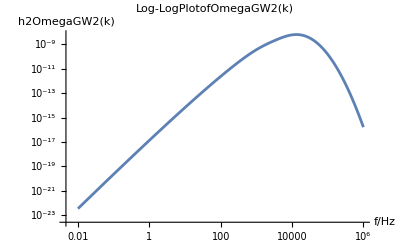

```mathematica
"First we import the data from the power spectrum file."
```

```mathematica
filePath = StringJoin["1e8g_NewFitted", "_PowerSpectrum.txt"]; data = Import[filePath, "Data"];
```

If you want to extract the individual columns for further processing.

```mathematica
frequencies = data[[All,1]]; MSPowerSolutions1 = data[[All,2]];
```

For example,you can create a plot.

```mathematica
Expr = ListLogLogPlot[Transpose[{frequencies, MSPowerSolutions1}], Joined -> True, AxesLabel -> {"f/Hz", "h2OmegaGW2(k)"}, PlotLabel -> "Log-Log Plot of OmegaGW2(k)", PlotRange -> {Automatic, Automatic}];
```

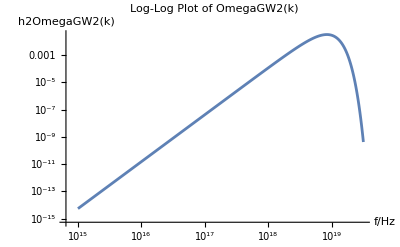

Constants and Functions.

```mathematica
MSPowerSolutions = Transpose[{frequencies, MSPowerSolutions1}]; cg = 0.4; OmegaR0 = 2.47/10^5; Ic[d_, s_] := -36*Pi*((s^2 + d^2 - 2)^2/(s^2 - d^2)^3)*UnitStep[s - 1]; Is[d_, s_] := -36*((s^2 + d^2 - 2)/(s^2 - d^2)^2)*(((s^2 + d^2 - 2)/(s^2 - d^2))*Log[(1 - d^2)/Abs[s^2 - 1]] + 2);
```

Interpolate the power spectrum so we have P as a function of k.

```mathematica
LogPInterpolation = Interpolation[Log10[MSPowerSolutions], InterpolationOrder -> 1]; P[k_] := 10^LogPInterpolation[Log10[k]]; kMin = Min[MSPowerSolutions[[All,1]]]; kMax = Max[MSPowerSolutions[[All,1]]];
```

Plot P[k] over the range of k values.

```mathematica
Expr = LogLogPlot[P[k], {k, kMin, kMax}, PlotRange -> All, AxesLabel -> {"k", "P(k)"}, PlotLabel -> "PowerSpectrumP(k)", GridLines -> Automatic];
```

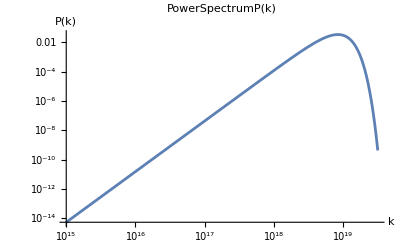

Calculate GW signature.

```mathematica
Integrand2[k_, d_, s_] := ((d^2 - 1/3)*((s^2 - 1/3)/(s^2 - d^2)))^2*P[k*Sqrt[3]*((s + d)/2)]*P[k*Sqrt[3]*((s - d)/2)]*(Is[d, s]^2 + Ic[d, s]^2); h2OmegaGW2[k_] := cg*(OmegaR0/36)*NIntegrate[Integrand2[k, d, s], {d, 0, 1/Sqrt[3]}, {s, 1/Sqrt[3], Infinity}, WorkingPrecision -> 40];
```

Local Adaptive can often taken a while to run, in which case Adaptive Monte Carlo is recommended for quick but reliable estimates.

Frequency region to plot GW signature in.

```mathematica
lowF = 10^(-2); highF = 10^6; conv = 1.546/10^15; k1 = 10^Range[Log10[lowF/conv], Log10[highF/conv], (Log10[highF/conv] - Log10[lowF/conv])/1000];
```

{6.46831×10^12,6.58856×10^12,6.71105×10^12,6.83582×10^12,6.96291×10^12,7.09236×10^12,7.22421×10^12,7.35852×10^12,7.49533×10^12,7.63467×10^12,7.77661×10^12,7.92119×10^12,8.06846×10^12,8.21846×10^12,8.37125×10^12,8.52689×10^12,8.68541×10^12,8.84689×10^12,9.01136×10^12,9.1789×10^12,9.34955×10^12,9.52337×10^12,9.70042×10^12,9.88076×10^12,1.00645×10^13,1.02516×10^13,1.04422×10^13,1.06363×10^13,1.0834×10^13,1.10355×10^13,1.12406×10^13,1.14496×10^13,1.16625×10^13,1.18793×10^13,1.21001×10^13,1.23251×10^13,1.25542×10^13,1.27876×10^13,1.30254×10^13,1.32675×10^13,1.35142×10^13,1.37655×10^13,1.40214×10^13,1.4282×10^13,1.45476×10^13,1.4818×10^13,1.50935×10^13,1.53741×10^13,1.566×10^13,1.59511×10^13,1.62476×10^13,1.65497×10^13,1.68574×10^13,1.71708×10^13,1.749×10^13,1.78152×10^13,1.81464×10^13,1.84838×10^13,1.88274×10^13,1.91774×10^13,1.9534×10^13,1.98971×10^13,2.0267×10^13,2.06438×10^13,2.10276×10^13,2.14186×10^13,2.18168×10^13,2.22224×10^13,2.26355×10^13,2.30563×10^13,2.3485×10^13,2.39216×10^13,2.43664×10^13,2.48194×10^13,2.52808×10^13,2.57508×10^13,2.62295×10^13,2.67172×10^13,2.72139×10^13,2.77198×10^13,2.82352×10^13,2.87601×10^13,2.92948×10^13,2.98394×10^13,3.03942×10^13,3.09593×10^13,3.15348×10^13,3.21211×10^13,3.27183×10^13,3.33266×10^13,3.39461×10^13,3.45773×10^13,3.52201×10^13,3.58749×10^13,3.65418×10^13,3.72212×10^13,3.79132×10^13,3.86181×10^13,3.9336×10^13,4.00673×10^13,4.08122×10^13,4.1571×10^13,4.23439×10^13,4.31311×10^13,4.3933×10^13,4.47497×10^13,4.55817×10^13,4.64291×10^13,4.72923×10^13,4.81715×10^13,4.90671×10^13,4.99793×10^13,5.09085×10^13,5.1855×10^13,5.2819×10^13,5.3801×10^13,5.48013×10^13,5.58201×10^13,5.68579×10^13,5.79149×10^13,5.89916×10^13,6.00884×10^13,6.12055×10^13,6.23434×10^13,6.35025×10^13,6.46831×10^13,6.58856×10^13,6.71105×10^13,6.83582×10^13,6.96291×10^13,7.09236×10^13,7.22421×10^13,7.35852×10^13,7.49533×10^13,7.63467×10^13,7.77661×10^13,7.92119×10^13,8.06846×10^13,8.21846×10^13,8.37125×10^13,8.52689×10^13,8.68541×10^13,8.84689×10^13,9.01136×10^13,9.1789×10^13,9.34955×10^13,9.52337×10^13,9.70042×10^13,9.88076×10^13,1.00645×10^14,1.02516×10^14,1.04422×10^14,1.06363×10^14,1.0834×10^14,1.10355×10^14,1.12406×10^14,1.14496×10^14,1.16625×10^14,1.18793×10^14,1.21001×10^14,1.23251×10^14,1.25542×10^14,1.27876×10^14,1.30254×10^14,1.32675×10^14,1.35142×10^14,1.37655×10^14,1.40214×10^14,1.4282×10^14,1.45476×10^14,1.4818×10^14,1.50935×10^14,1.53741×10^14,1.566×10^14,1.59511×10^14,1.62476×10^14,1.65497×10^14,1.68574×10^14,1.71708×10^14,1.749×10^14,1.78152×10^14,1.81464×10^14,1.84838×10^14,1.88274×10^14,1.91774×10^14,1.9534×10^14,1.98971×10^14,2.0267×10^14,2.06438×10^14,2.10276×10^14,2.14186×10^14,2.18168×10^14,2.22224×10^14,2.26355×10^14,2.30563×10^14,2.3485×10^14,2.39216×10^14,2.43664×10^14,2.48194×10^14,2.52808×10^14,2.57508×10^14,2.62295×10^14,2.67172×10^14,2.72139×10^14,2.77198×10^14,2.82352×10^14,2.87601×10^14,2.92948×10^14,2.98394×10^14,3.03942×10^14,3.09593×10^14,3.15348×10^14,3.21211×10^14,3.27183×10^14,3.33266×10^14,3.39461×10^14,3.45773×10^14,3.52201×10^14,3.58749×10^14,3.65418×10^14,3.72212×10^14,3.79132×10^14,3.86181×10^14,3.9336×10^14,4.00673×10^14,4.08122×10^14,4.1571×10^14,4.23439×10^14,4.31311×10^14,4.3933×10^14,4.47497×10^14,4.55817×10^14,4.64291×10^14,4.72923×10^14,4.81715×10^14,4.90671×10^14,4.99793×10^14,5.09085×10^14,5.1855×10^14,5.2819×10^14,5.3801×10^14,5.48013×10^14,5.58201×10^14,5.68579×10^14,5.79149×10^14,5.89916×10^14,6.00884×10^14,6.12055×10^14,6.23434×10^14,6.35025×10^14,6.46831×10^14,6.58856×10^14,6.71105×10^14,6.83582×10^14,6.96291×10^14,7.09236×10^14,7.22421×10^14,7.35852×10^14,7.49533×10^14,7.63467×10^14,7.77661×10^14,7.92119×10^14,8.06846×10^14,8.21846×10^14,8.37125×10^14,8.52689×10^14,8.68541×10^14,8.84689×10^14,9.01136×10^14,9.1789×10^14,9.34955×10^14,9.52337×10^14,9.70042×10^14,9.88076×10^14,1.00645×10^15,1.02516×10^15,1.04422×10^15,1.06363×10^15,1.0834×10^15,1.10355×10^15,1.12406×10^15,1.14496×10^15,1.16625×10^15,1.18793×10^15,1.21001×10^15,1.23251×10^15,1.25542×10^15,1.27876×10^15,1.30254×10^15,1.32675×10^15,1.35142×10^15,1.37655×10^15,1.40214×10^15,1.4282×10^15,1.45476×10^15,1.4818×10^15,1.50935×10^15,1.53741×10^15,1.566×10^15,1.59511×10^15,1.62476×10^15,1.65497×10^15,1.68574×10^15,1.71708×10^15,1.749×10^15,1.78152×10^15,1.81464×10^15,1.84838×10^15,1.88274×10^15,1.91774×10^15,1.9534×10^15,1.98971×10^15,2.0267×10^15,2.06438×10^15,2.10276×10^15,2.14186×10^15,2.18168×10^15,2.22224×10^15,2.26355×10^15,2.30563×10^15,2.3485×10^15,2.39216×10^15,2.43664×10^15,2.48194×10^15,2.52808×10^15,2.57508×10^15,2.62295×10^15,2.67172×10^15,2.72139×10^15,2.77198×10^15,2.82352×10^15,2.87601×10^15,2.92948×10^15,2.98394×10^15,3.03942×10^15,3.09593×10^15,3.15348×10^15,3.21211×10^15,3.27183×10^15,3.33266×10^15,3.39461×10^15,3.45773×10^15,3.52201×10^15,3.58749×10^15,3.65418×10^15,3.72212×10^15,3.79132×10^15,3.86181×10^15,3.9336×10^15,4.00673×10^15,4.08122×10^15,4.1571×10^15,4.23439×10^15,4.31311×10^15,4.3933×10^15,4.47497×10^15,4.55817×10^15,4.64291×10^15,4.72923×10^15,4.81715×10^15,4.90671×10^15,4.99793×10^15,5.09085×10^15,5.1855×10^15,5.2819×10^15,5.3801×10^15,5.48013×10^15,5.58201×10^15,5.68579×10^15,5.79149×10^15,5.89916×10^15,6.00884×10^15,6.12055×10^15,6.23434×10^15,6.35025×10^15,6.46831×10^15,6.58856×10^15,6.71105×10^15,6.83582×10^15,6.96291×10^15,7.09236×10^15,7.22421×10^15,7.35852×10^15,7.49533×10^15,7.63467×10^15,7.77661×10^15,7.92119×10^15,8.06846×10^15,8.21846×10^15,8.37125×10^15,8.52689×10^15,8.68541×10^15,8.84689×10^15,9.01136×10^15,9.1789×10^15,9.34955×10^15,9.52337×10^15,9.70042×10^15,9.88076×10^15,1.00645×10^16,1.02516×10^16,1.04422×10^16,1.06363×10^16,1.0834×10^16,1.10355×10^16,1.12406×10^16,1.14496×10^16,1.16625×10^16,1.18793×10^16,1.21001×10^16,1.23251×10^16,1.25542×10^16,1.27876×10^16,1.30254×10^16,1.32675×10^16,1.35142×10^16,1.37655×10^16,1.40214×10^16,1.4282×10^16,1.45476×10^16,1.4818×10^16,1.50935×10^16,1.53741×10^16,1.566×10^16,1.59511×10^16,1.62476×10^16,1.65497×10^16,1.68574×10^16,1.71708×10^16,1.749×10^16,1.78152×10^16,1.81464×10^16,1.84838×10^16,1.88274×10^16,1.91774×10^16,1.9534×10^16,1.98971×10^16,2.0267×10^16,2.06438×10^16,2.10276×10^16,2.14186×10^16,2.18168×10^16,2.22224×10^16,2.26355×10^16,2.30563×10^16,2.3485×10^16,2.39216×10^16,2.43664×10^16,2.48194×10^16,2.52808×10^16,2.57508×10^16,2.62295×10^16,2.67172×10^16,2.72139×10^16,2.77198×10^16,2.82352×10^16,2.87601×10^16,2.92948×10^16,2.98394×10^16,3.03942×10^16,3.09593×10^16,3.15348×10^16,3.21211×10^16,3.27183×10^16,3.33266×10^16,3.39461×10^16,3.45773×10^16,3.52201×10^16,3.58749×10^16,3.65418×10^16,3.72212×10^16,3.79132×10^16,3.86181×10^16,3.9336×10^16,4.00673×10^16,4.08122×10^16,4.1571×10^16,4.23439×10^16,4.31311×10^16,4.3933×10^16,4.47497×10^16,4.55817×10^16,4.64291×10^16,4.72923×10^16,4.81715×10^16,4.90671×10^16,4.99793×10^16,5.09085×10^16,5.1855×10^16,5.2819×10^16,5.3801×10^16,5.48013×10^16,5.58201×10^16,5.68579×10^16,5.79149×10^16,5.89916×10^16,6.00884×10^16,6.12055×10^16,6.23434×10^16,6.35025×10^16,6.46831×10^16,6.58856×10^16,6.71105×10^16,6.83582×10^16,6.96291×10^16,7.09236×10^16,7.22421×10^16,7.35852×10^16,7.49533×10^16,7.63467×10^16,7.77661×10^16,7.92119×10^16,8.06846×10^16,8.21846×10^16,8.37125×10^16,8.52689×10^16,8.68541×10^16,8.84689×10^16,9.01136×10^16,9.1789×10^16,9.34955×10^16,9.52337×10^16,9.70042×10^16,9.88076×10^16,1.00645×10^17,1.02516×10^17,1.04422×10^17,1.06363×10^17,1.0834×10^17,1.10355×10^17,1.12406×10^17,1.14496×10^17,1.16625×10^17,1.18793×10^17,1.21001×10^17,1.23251×10^17,1.25542×10^17,1.27876×10^17,1.30254×10^17,1.32675×10^17,1.35142×10^17,1.37655×10^17,1.40214×10^17,1.4282×10^17,1.45476×10^17,1.4818×10^17,1.50935×10^17,1.53741×10^17,1.566×10^17,1.59511×10^17,1.62476×10^17,1.65497×10^17,1.68574×10^17,1.71708×10^17,1.749×10^17,1.78152×10^17,1.81464×10^17,1.84838×10^17,1.88274×10^17,1.91774×10^17,1.9534×10^17,1.98971×10^17,2.0267×10^17,2.06438×10^17,2.10276×10^17,2.14186×10^17,2.18168×10^17,2.22224×10^17,2.26355×10^17,2.30563×10^17,2.3485×10^17,2.39216×10^17,2.43664×10^17,2.48194×10^17,2.52808×10^17,2.57508×10^17,2.62295×10^17,2.67172×10^17,2.72139×10^17,2.77198×10^17,2.82352×10^17,2.87601×10^17,2.92948×10^17,2.98394×10^17,3.03942×10^17,3.09593×10^17,3.15348×10^17,3.21211×10^17,3.27183×10^17,3.33266×10^17,3.39461×10^17,3.45773×10^17,3.52201×10^17,3.58749×10^17,3.65418×10^17,3.72212×10^17,3.79132×10^17,3.86181×10^17,3.9336×10^17,4.00673×10^17,4.08122×10^17,4.1571×10^17,4.23439×10^17,4.31311×10^17,4.3933×10^17,4.47497×10^17,4.55817×10^17,4.64291×10^17,4.72923×10^17,4.81715×10^17,4.90671×10^17,4.99793×10^17,5.09085×10^17,5.1855×10^17,5.2819×10^17,5.3801×10^17,5.48013×10^17,5.58201×10^17,5.68579×10^17,5.79149×10^17,5.89916×10^17,6.00884×10^17,6.12055×10^17,6.23434×10^17,6.35025×10^17,6.46831×10^17,6.58856×10^17,6.71105×10^17,6.83582×10^17,6.96291×10^17,7.09236×10^17,7.22421×10^17,7.35852×10^17,7.49533×10^17,7.63467×10^17,7.77661×10^17,7.92119×10^17,8.06846×10^17,8.21846×10^17,8.37125×10^17,8.52689×10^17,8.68541×10^17,8.84689×10^17,9.01136×10^17,9.1789×10^17,9.34955×10^17,9.52337×10^17,9.70042×10^17,9.88076×10^17,1.00645×10^18,1.02516×10^18,1.04422×10^18,1.06363×10^18,1.0834×10^18,1.10355×10^18,1.12406×10^18,1.14496×10^18,1.16625×10^18,1.18793×10^18,1.21001×10^18,1.23251×10^18,1.25542×10^18,1.27876×10^18,1.30254×10^18,1.32675×10^18,1.35142×10^18,1.37655×10^18,1.40214×10^18,1.4282×10^18,1.45476×10^18,1.4818×10^18,1.50935×10^18,1.53741×10^18,1.566×10^18,1.59511×10^18,1.62476×10^18,1.65497×10^18,1.68574×10^18,1.71708×10^18,1.749×10^18,1.78152×10^18,1.81464×10^18,1.84838×10^18,1.88274×10^18,1.91774×10^18,1.9534×10^18,1.98971×10^18,2.0267×10^18,2.06438×10^18,2.10276×10^18,2.14186×10^18,2.18168×10^18,2.22224×10^18,2.26355×10^18,2.30563×10^18,2.3485×10^18,2.39216×10^18,2.43664×10^18,2.48194×10^18,2.52808×10^18,2.57508×10^18,2.62295×10^18,2.67172×10^18,2.72139×10^18,2.77198×10^18,2.82352×10^18,2.87601×10^18,2.92948×10^18,2.98394×10^18,3.03942×10^18,3.09593×10^18,3.15348×10^18,3.21211×10^18,3.27183×10^18,3.33266×10^18,3.39461×10^18,3.45773×10^18,3.52201×10^18,3.58749×10^18,3.65418×10^18,3.72212×10^18,3.79132×10^18,3.86181×10^18,3.9336×10^18,4.00673×10^18,4.08122×10^18,4.1571×10^18,4.23439×10^18,4.31311×10^18,4.3933×10^18,4.47497×10^18,4.55817×10^18,4.64291×10^18,4.72923×10^18,4.81715×10^18,4.90671×10^18,4.99793×10^18,5.09085×10^18,5.1855×10^18,5.2819×10^18,5.3801×10^18,5.48013×10^18,5.58201×10^18,5.68579×10^18,5.79149×10^18,5.89916×10^18,6.00884×10^18,6.12055×10^18,6.23434×10^18,6.35025×10^18,6.46831×10^18,6.58856×10^18,6.71105×10^18,6.83582×10^18,6.96291×10^18,7.09236×10^18,7.22421×10^18,7.35852×10^18,7.49533×10^18,7.63467×10^18,7.77661×10^18,7.92119×10^18,8.06846×10^18,8.21846×10^18,8.37125×10^18,8.52689×10^18,8.68541×10^18,8.84689×10^18,9.01136×10^18,9.1789×10^18,9.34955×10^18,9.52337×10^18,9.70042×10^18,9.88076×10^18,1.00645×10^19,1.02516×10^19,1.04422×10^19,1.06363×10^19,1.0834×10^19,1.10355×10^19,1.12406×10^19,1.14496×10^19,1.16625×10^19,1.18793×10^19,1.21001×10^19,1.23251×10^19,1.25542×10^19,1.27876×10^19,1.30254×10^19,1.32675×10^19,1.35142×10^19,1.37655×10^19,1.40214×10^19,1.4282×10^19,1.45476×10^19,1.4818×10^19,1.50935×10^19,1.53741×10^19,1.566×10^19,1.59511×10^19,1.62476×10^19,1.65497×10^19,1.68574×10^19,1.71708×10^19,1.749×10^19,1.78152×10^19,1.81464×10^19,1.84838×10^19,1.88274×10^19,1.91774×10^19,1.9534×10^19,1.98971×10^19,2.0267×10^19,2.06438×10^19,2.10276×10^19,2.14186×10^19,2.18168×10^19,2.22224×10^19,2.26355×10^19,2.30563×10^19,2.3485×10^19,2.39216×10^19,2.43664×10^19,2.48194×10^19,2.52808×10^19,2.57508×10^19,2.62295×10^19,2.67172×10^19,2.72139×10^19,2.77198×10^19,2.82352×10^19,2.87601×10^19,2.92948×10^19,2.98394×10^19,3.03942×10^19,3.09593×10^19,3.15348×10^19,3.21211×10^19,3.27183×10^19,3.33266×10^19,3.39461×10^19,3.45773×10^19,3.52201×10^19,3.58749×10^19,3.65418×10^19,3.72212×10^19,3.79132×10^19,3.86181×10^19,3.9336×10^19,4.00673×10^19,4.08122×10^19,4.1571×10^19,4.23439×10^19,4.31311×10^19,4.3933×10^19,4.47497×10^19,4.55817×10^19,4.64291×10^19,4.72923×10^19,4.81715×10^19,4.90671×10^19,4.99793×10^19,5.09085×10^19,5.1855×10^19,5.2819×10^19,5.3801×10^19,5.48013×10^19,5.58201×10^19,5.68579×10^19,5.79149×10^19,5.89916×10^19,6.00884×10^19,6.12055×10^19,6.23434×10^19,6.35025×10^19,6.46831×10^19,6.58856×10^19,6.71105×10^19,6.83582×10^19,6.96291×10^19,7.09236×10^19,7.22421×10^19,7.35852×10^19,7.49533×10^19,7.63467×10^19,7.77661×10^19,7.92119×10^19,8.06846×10^19,8.21846×10^19,8.37125×10^19,8.52689×10^19,8.68541×10^19,8.84689×10^19,9.01136×10^19,9.1789×10^19,9.34955×10^19,9.52337×10^19,9.70042×10^19,9.88076×10^19,1.00645×10^20,1.02516×10^20,1.04422×10^20,1.06363×10^20,1.0834×10^20,1.10355×10^20,1.12406×10^20,1.14496×10^20,1.16625×10^20,1.18793×10^20,1.21001×10^20,1.23251×10^20,1.25542×10^20,1.27876×10^20,1.30254×10^20,1.32675×10^20,1.35142×10^20,1.37655×10^20,1.40214×10^20,1.4282×10^20,1.45476×10^20,1.4818×10^20,1.50935×10^20,1.53741×10^20,1.566×10^20,1.59511×10^20,1.62476×10^20,1.65497×10^20,1.68574×10^20,1.71708×10^20,1.749×10^20,1.78152×10^20,1.81464×10^20,1.84838×10^20,1.88274×10^20,1.91774×10^20,1.9534×10^20,1.98971×10^20,2.0267×10^20,2.06438×10^20,2.10276×10^20,2.14186×10^20,2.18168×10^20,2.22224×10^20,2.26355×10^20,2.30563×10^20,2.3485×10^20,2.39216×10^20,2.43664×10^20,2.48194×10^20,2.52808×10^20,2.57508×10^20,2.62295×10^20,2.67172×10^20,2.72139×10^20,2.77198×10^20,2.82352×10^20,2.87601×10^20,2.92948×10^20,2.98394×10^20,3.03942×10^20,3.09593×10^20,3.15348×10^20,3.21211×10^20,3.27183×10^20,3.33266×10^20,3.39461×10^20,3.45773×10^20,3.52201×10^20,3.58749×10^20,3.65418×10^20,3.72212×10^20,3.79132×10^20,3.86181×10^20,3.9336×10^20,4.00673×10^20,4.08122×10^20,4.1571×10^20,4.23439×10^20,4.31311×10^20,4.3933×10^20,4.47497×10^20,4.55817×10^20,4.64291×10^20,4.72923×10^20,4.81715×10^20,4.90671×10^20,4.99793×10^20,5.09085×10^20,5.1855×10^20,5.2819×10^20,5.3801×10^20,5.48013×10^20,5.58201×10^20,5.68579×10^20,5.79149×10^20,5.89916×10^20,6.00884×10^20,6.12055×10^20,6.23434×10^20,6.35025×10^20,6.46831×10^20}

Calculate the GW signature for the given frequency range.

```mathematica
Get[FileNameJoin[{Directory[], StringJoin["1e8g_NewFitted", "_GW.mx"]}]];
```

Plot.

```mathematica
Expr = ListLogLogPlot[Transpose[{conv*k1, h2OmegaGW2Sol}], Joined -> True, AxesLabel -> {"f/Hz", "h2OmegaGW2(k)"}, PlotLabel -> "Log-LogPlotofOmegaGW2(k)", PlotRange -> {Automatic, Automatic}]; Export[StringJoin["1e8g_NewFitted", "_GW.csv"], Transpose[{conv*k1, h2OmegaGW2Sol}], "CSV"];
```

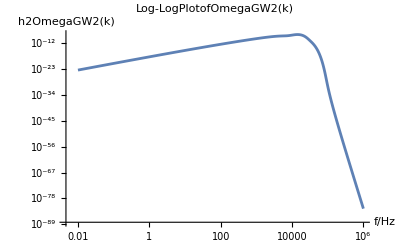

```mathematica
"First we import the data from the power spectrum file."
```

```mathematica
filePath = StringJoin["1e8g_NewFitted_n_4", "_PowerSpectrum.txt"]; data = Import[filePath, "Data"];
```

If you want to extract the individual columns for further processing.

```mathematica
frequencies = data[[All,1]]; MSPowerSolutions1 = data[[All,2]];
```

For example,you can create a plot.

```mathematica
Expr = ListLogLogPlot[Transpose[{frequencies, MSPowerSolutions1}], Joined -> True, AxesLabel -> {"f/Hz", "h2OmegaGW2(k)"}, PlotLabel -> "Log-Log Plot of OmegaGW2(k)", PlotRange -> {Automatic, Automatic}];
```

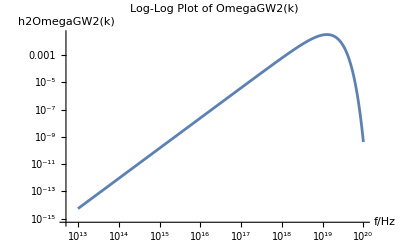

Constants and Functions.

```mathematica
MSPowerSolutions = Transpose[{frequencies, MSPowerSolutions1}]; cg = 0.4; OmegaR0 = 2.47/10^5; Ic[d_, s_] := -36*Pi*((s^2 + d^2 - 2)^2/(s^2 - d^2)^3)*UnitStep[s - 1]; Is[d_, s_] := -36*((s^2 + d^2 - 2)/(s^2 - d^2)^2)*(((s^2 + d^2 - 2)/(s^2 - d^2))*Log[(1 - d^2)/Abs[s^2 - 1]] + 2);
```

Interpolate the power spectrum so we have P as a function of k.

```mathematica
LogPInterpolation = Interpolation[Log10[MSPowerSolutions], InterpolationOrder -> 1]; P[k_] := 10^LogPInterpolation[Log10[k]]; kMin = Min[MSPowerSolutions[[All,1]]]; kMax = Max[MSPowerSolutions[[All,1]]];
```

Plot P[k] over the range of k values.

```mathematica
Expr = LogLogPlot[P[k], {k, kMin, kMax}, PlotRange -> All, AxesLabel -> {"k", "P(k)"}, PlotLabel -> "PowerSpectrumP(k)", GridLines -> Automatic];
```

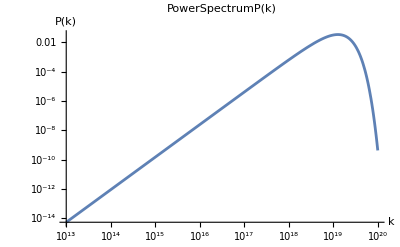

Calculate GW signature.

```mathematica
Integrand2[k_, d_, s_] := ((d^2 - 1/3)*((s^2 - 1/3)/(s^2 - d^2)))^2*P[k*Sqrt[3]*((s + d)/2)]*P[k*Sqrt[3]*((s - d)/2)]*(Is[d, s]^2 + Ic[d, s]^2); h2OmegaGW2[k_] := cg*(OmegaR0/36)*NIntegrate[Integrand2[k, d, s], {d, 0, 1/Sqrt[3]}, {s, 1/Sqrt[3], Infinity}, WorkingPrecision -> 40];
```

Local Adaptive can often taken a while to run, in which case Adaptive Monte Carlo is recommended for quick but reliable estimates.

Frequency region to plot GW signature in.

```mathematica
lowF = 10^(-2); highF = 10^6; conv = 1.546/10^15; k1 = 10^Range[Log10[lowF/conv], Log10[highF/conv], (Log10[highF/conv] - Log10[lowF/conv])/1000];
```

{6.46831×10^12,6.58856×10^12,6.71105×10^12,6.83582×10^12,6.96291×10^12,7.09236×10^12,7.22421×10^12,7.35852×10^12,7.49533×10^12,7.63467×10^12,7.77661×10^12,7.92119×10^12,8.06846×10^12,8.21846×10^12,8.37125×10^12,8.52689×10^12,8.68541×10^12,8.84689×10^12,9.01136×10^12,9.1789×10^12,9.34955×10^12,9.52337×10^12,9.70042×10^12,9.88076×10^12,1.00645×10^13,1.02516×10^13,1.04422×10^13,1.06363×10^13,1.0834×10^13,1.10355×10^13,1.12406×10^13,1.14496×10^13,1.16625×10^13,1.18793×10^13,1.21001×10^13,1.23251×10^13,1.25542×10^13,1.27876×10^13,1.30254×10^13,1.32675×10^13,1.35142×10^13,1.37655×10^13,1.40214×10^13,1.4282×10^13,1.45476×10^13,1.4818×10^13,1.50935×10^13,1.53741×10^13,1.566×10^13,1.59511×10^13,1.62476×10^13,1.65497×10^13,1.68574×10^13,1.71708×10^13,1.749×10^13,1.78152×10^13,1.81464×10^13,1.84838×10^13,1.88274×10^13,1.91774×10^13,1.9534×10^13,1.98971×10^13,2.0267×10^13,2.06438×10^13,2.10276×10^13,2.14186×10^13,2.18168×10^13,2.22224×10^13,2.26355×10^13,2.30563×10^13,2.3485×10^13,2.39216×10^13,2.43664×10^13,2.48194×10^13,2.52808×10^13,2.57508×10^13,2.62295×10^13,2.67172×10^13,2.72139×10^13,2.77198×10^13,2.82352×10^13,2.87601×10^13,2.92948×10^13,2.98394×10^13,3.03942×10^13,3.09593×10^13,3.15348×10^13,3.21211×10^13,3.27183×10^13,3.33266×10^13,3.39461×10^13,3.45773×10^13,3.52201×10^13,3.58749×10^13,3.65418×10^13,3.72212×10^13,3.79132×10^13,3.86181×10^13,3.9336×10^13,4.00673×10^13,4.08122×10^13,4.1571×10^13,4.23439×10^13,4.31311×10^13,4.3933×10^13,4.47497×10^13,4.55817×10^13,4.64291×10^13,4.72923×10^13,4.81715×10^13,4.90671×10^13,4.99793×10^13,5.09085×10^13,5.1855×10^13,5.2819×10^13,5.3801×10^13,5.48013×10^13,5.58201×10^13,5.68579×10^13,5.79149×10^13,5.89916×10^13,6.00884×10^13,6.12055×10^13,6.23434×10^13,6.35025×10^13,6.46831×10^13,6.58856×10^13,6.71105×10^13,6.83582×10^13,6.96291×10^13,7.09236×10^13,7.22421×10^13,7.35852×10^13,7.49533×10^13,7.63467×10^13,7.77661×10^13,7.92119×10^13,8.06846×10^13,8.21846×10^13,8.37125×10^13,8.52689×10^13,8.68541×10^13,8.84689×10^13,9.01136×10^13,9.1789×10^13,9.34955×10^13,9.52337×10^13,9.70042×10^13,9.88076×10^13,1.00645×10^14,1.02516×10^14,1.04422×10^14,1.06363×10^14,1.0834×10^14,1.10355×10^14,1.12406×10^14,1.14496×10^14,1.16625×10^14,1.18793×10^14,1.21001×10^14,1.23251×10^14,1.25542×10^14,1.27876×10^14,1.30254×10^14,1.32675×10^14,1.35142×10^14,1.37655×10^14,1.40214×10^14,1.4282×10^14,1.45476×10^14,1.4818×10^14,1.50935×10^14,1.53741×10^14,1.566×10^14,1.59511×10^14,1.62476×10^14,1.65497×10^14,1.68574×10^14,1.71708×10^14,1.749×10^14,1.78152×10^14,1.81464×10^14,1.84838×10^14,1.88274×10^14,1.91774×10^14,1.9534×10^14,1.98971×10^14,2.0267×10^14,2.06438×10^14,2.10276×10^14,2.14186×10^14,2.18168×10^14,2.22224×10^14,2.26355×10^14,2.30563×10^14,2.3485×10^14,2.39216×10^14,2.43664×10^14,2.48194×10^14,2.52808×10^14,2.57508×10^14,2.62295×10^14,2.67172×10^14,2.72139×10^14,2.77198×10^14,2.82352×10^14,2.87601×10^14,2.92948×10^14,2.98394×10^14,3.03942×10^14,3.09593×10^14,3.15348×10^14,3.21211×10^14,3.27183×10^14,3.33266×10^14,3.39461×10^14,3.45773×10^14,3.52201×10^14,3.58749×10^14,3.65418×10^14,3.72212×10^14,3.79132×10^14,3.86181×10^14,3.9336×10^14,4.00673×10^14,4.08122×10^14,4.1571×10^14,4.23439×10^14,4.31311×10^14,4.3933×10^14,4.47497×10^14,4.55817×10^14,4.64291×10^14,4.72923×10^14,4.81715×10^14,4.90671×10^14,4.99793×10^14,5.09085×10^14,5.1855×10^14,5.2819×10^14,5.3801×10^14,5.48013×10^14,5.58201×10^14,5.68579×10^14,5.79149×10^14,5.89916×10^14,6.00884×10^14,6.12055×10^14,6.23434×10^14,6.35025×10^14,6.46831×10^14,6.58856×10^14,6.71105×10^14,6.83582×10^14,6.96291×10^14,7.09236×10^14,7.22421×10^14,7.35852×10^14,7.49533×10^14,7.63467×10^14,7.77661×10^14,7.92119×10^14,8.06846×10^14,8.21846×10^14,8.37125×10^14,8.52689×10^14,8.68541×10^14,8.84689×10^14,9.01136×10^14,9.1789×10^14,9.34955×10^14,9.52337×10^14,9.70042×10^14,9.88076×10^14,1.00645×10^15,1.02516×10^15,1.04422×10^15,1.06363×10^15,1.0834×10^15,1.10355×10^15,1.12406×10^15,1.14496×10^15,1.16625×10^15,1.18793×10^15,1.21001×10^15,1.23251×10^15,1.25542×10^15,1.27876×10^15,1.30254×10^15,1.32675×10^15,1.35142×10^15,1.37655×10^15,1.40214×10^15,1.4282×10^15,1.45476×10^15,1.4818×10^15,1.50935×10^15,1.53741×10^15,1.566×10^15,1.59511×10^15,1.62476×10^15,1.65497×10^15,1.68574×10^15,1.71708×10^15,1.749×10^15,1.78152×10^15,1.81464×10^15,1.84838×10^15,1.88274×10^15,1.91774×10^15,1.9534×10^15,1.98971×10^15,2.0267×10^15,2.06438×10^15,2.10276×10^15,2.14186×10^15,2.18168×10^15,2.22224×10^15,2.26355×10^15,2.30563×10^15,2.3485×10^15,2.39216×10^15,2.43664×10^15,2.48194×10^15,2.52808×10^15,2.57508×10^15,2.62295×10^15,2.67172×10^15,2.72139×10^15,2.77198×10^15,2.82352×10^15,2.87601×10^15,2.92948×10^15,2.98394×10^15,3.03942×10^15,3.09593×10^15,3.15348×10^15,3.21211×10^15,3.27183×10^15,3.33266×10^15,3.39461×10^15,3.45773×10^15,3.52201×10^15,3.58749×10^15,3.65418×10^15,3.72212×10^15,3.79132×10^15,3.86181×10^15,3.9336×10^15,4.00673×10^15,4.08122×10^15,4.1571×10^15,4.23439×10^15,4.31311×10^15,4.3933×10^15,4.47497×10^15,4.55817×10^15,4.64291×10^15,4.72923×10^15,4.81715×10^15,4.90671×10^15,4.99793×10^15,5.09085×10^15,5.1855×10^15,5.2819×10^15,5.3801×10^15,5.48013×10^15,5.58201×10^15,5.68579×10^15,5.79149×10^15,5.89916×10^15,6.00884×10^15,6.12055×10^15,6.23434×10^15,6.35025×10^15,6.46831×10^15,6.58856×10^15,6.71105×10^15,6.83582×10^15,6.96291×10^15,7.09236×10^15,7.22421×10^15,7.35852×10^15,7.49533×10^15,7.63467×10^15,7.77661×10^15,7.92119×10^15,8.06846×10^15,8.21846×10^15,8.37125×10^15,8.52689×10^15,8.68541×10^15,8.84689×10^15,9.01136×10^15,9.1789×10^15,9.34955×10^15,9.52337×10^15,9.70042×10^15,9.88076×10^15,1.00645×10^16,1.02516×10^16,1.04422×10^16,1.06363×10^16,1.0834×10^16,1.10355×10^16,1.12406×10^16,1.14496×10^16,1.16625×10^16,1.18793×10^16,1.21001×10^16,1.23251×10^16,1.25542×10^16,1.27876×10^16,1.30254×10^16,1.32675×10^16,1.35142×10^16,1.37655×10^16,1.40214×10^16,1.4282×10^16,1.45476×10^16,1.4818×10^16,1.50935×10^16,1.53741×10^16,1.566×10^16,1.59511×10^16,1.62476×10^16,1.65497×10^16,1.68574×10^16,1.71708×10^16,1.749×10^16,1.78152×10^16,1.81464×10^16,1.84838×10^16,1.88274×10^16,1.91774×10^16,1.9534×10^16,1.98971×10^16,2.0267×10^16,2.06438×10^16,2.10276×10^16,2.14186×10^16,2.18168×10^16,2.22224×10^16,2.26355×10^16,2.30563×10^16,2.3485×10^16,2.39216×10^16,2.43664×10^16,2.48194×10^16,2.52808×10^16,2.57508×10^16,2.62295×10^16,2.67172×10^16,2.72139×10^16,2.77198×10^16,2.82352×10^16,2.87601×10^16,2.92948×10^16,2.98394×10^16,3.03942×10^16,3.09593×10^16,3.15348×10^16,3.21211×10^16,3.27183×10^16,3.33266×10^16,3.39461×10^16,3.45773×10^16,3.52201×10^16,3.58749×10^16,3.65418×10^16,3.72212×10^16,3.79132×10^16,3.86181×10^16,3.9336×10^16,4.00673×10^16,4.08122×10^16,4.1571×10^16,4.23439×10^16,4.31311×10^16,4.3933×10^16,4.47497×10^16,4.55817×10^16,4.64291×10^16,4.72923×10^16,4.81715×10^16,4.90671×10^16,4.99793×10^16,5.09085×10^16,5.1855×10^16,5.2819×10^16,5.3801×10^16,5.48013×10^16,5.58201×10^16,5.68579×10^16,5.79149×10^16,5.89916×10^16,6.00884×10^16,6.12055×10^16,6.23434×10^16,6.35025×10^16,6.46831×10^16,6.58856×10^16,6.71105×10^16,6.83582×10^16,6.96291×10^16,7.09236×10^16,7.22421×10^16,7.35852×10^16,7.49533×10^16,7.63467×10^16,7.77661×10^16,7.92119×10^16,8.06846×10^16,8.21846×10^16,8.37125×10^16,8.52689×10^16,8.68541×10^16,8.84689×10^16,9.01136×10^16,9.1789×10^16,9.34955×10^16,9.52337×10^16,9.70042×10^16,9.88076×10^16,1.00645×10^17,1.02516×10^17,1.04422×10^17,1.06363×10^17,1.0834×10^17,1.10355×10^17,1.12406×10^17,1.14496×10^17,1.16625×10^17,1.18793×10^17,1.21001×10^17,1.23251×10^17,1.25542×10^17,1.27876×10^17,1.30254×10^17,1.32675×10^17,1.35142×10^17,1.37655×10^17,1.40214×10^17,1.4282×10^17,1.45476×10^17,1.4818×10^17,1.50935×10^17,1.53741×10^17,1.566×10^17,1.59511×10^17,1.62476×10^17,1.65497×10^17,1.68574×10^17,1.71708×10^17,1.749×10^17,1.78152×10^17,1.81464×10^17,1.84838×10^17,1.88274×10^17,1.91774×10^17,1.9534×10^17,1.98971×10^17,2.0267×10^17,2.06438×10^17,2.10276×10^17,2.14186×10^17,2.18168×10^17,2.22224×10^17,2.26355×10^17,2.30563×10^17,2.3485×10^17,2.39216×10^17,2.43664×10^17,2.48194×10^17,2.52808×10^17,2.57508×10^17,2.62295×10^17,2.67172×10^17,2.72139×10^17,2.77198×10^17,2.82352×10^17,2.87601×10^17,2.92948×10^17,2.98394×10^17,3.03942×10^17,3.09593×10^17,3.15348×10^17,3.21211×10^17,3.27183×10^17,3.33266×10^17,3.39461×10^17,3.45773×10^17,3.52201×10^17,3.58749×10^17,3.65418×10^17,3.72212×10^17,3.79132×10^17,3.86181×10^17,3.9336×10^17,4.00673×10^17,4.08122×10^17,4.1571×10^17,4.23439×10^17,4.31311×10^17,4.3933×10^17,4.47497×10^17,4.55817×10^17,4.64291×10^17,4.72923×10^17,4.81715×10^17,4.90671×10^17,4.99793×10^17,5.09085×10^17,5.1855×10^17,5.2819×10^17,5.3801×10^17,5.48013×10^17,5.58201×10^17,5.68579×10^17,5.79149×10^17,5.89916×10^17,6.00884×10^17,6.12055×10^17,6.23434×10^17,6.35025×10^17,6.46831×10^17,6.58856×10^17,6.71105×10^17,6.83582×10^17,6.96291×10^17,7.09236×10^17,7.22421×10^17,7.35852×10^17,7.49533×10^17,7.63467×10^17,7.77661×10^17,7.92119×10^17,8.06846×10^17,8.21846×10^17,8.37125×10^17,8.52689×10^17,8.68541×10^17,8.84689×10^17,9.01136×10^17,9.1789×10^17,9.34955×10^17,9.52337×10^17,9.70042×10^17,9.88076×10^17,1.00645×10^18,1.02516×10^18,1.04422×10^18,1.06363×10^18,1.0834×10^18,1.10355×10^18,1.12406×10^18,1.14496×10^18,1.16625×10^18,1.18793×10^18,1.21001×10^18,1.23251×10^18,1.25542×10^18,1.27876×10^18,1.30254×10^18,1.32675×10^18,1.35142×10^18,1.37655×10^18,1.40214×10^18,1.4282×10^18,1.45476×10^18,1.4818×10^18,1.50935×10^18,1.53741×10^18,1.566×10^18,1.59511×10^18,1.62476×10^18,1.65497×10^18,1.68574×10^18,1.71708×10^18,1.749×10^18,1.78152×10^18,1.81464×10^18,1.84838×10^18,1.88274×10^18,1.91774×10^18,1.9534×10^18,1.98971×10^18,2.0267×10^18,2.06438×10^18,2.10276×10^18,2.14186×10^18,2.18168×10^18,2.22224×10^18,2.26355×10^18,2.30563×10^18,2.3485×10^18,2.39216×10^18,2.43664×10^18,2.48194×10^18,2.52808×10^18,2.57508×10^18,2.62295×10^18,2.67172×10^18,2.72139×10^18,2.77198×10^18,2.82352×10^18,2.87601×10^18,2.92948×10^18,2.98394×10^18,3.03942×10^18,3.09593×10^18,3.15348×10^18,3.21211×10^18,3.27183×10^18,3.33266×10^18,3.39461×10^18,3.45773×10^18,3.52201×10^18,3.58749×10^18,3.65418×10^18,3.72212×10^18,3.79132×10^18,3.86181×10^18,3.9336×10^18,4.00673×10^18,4.08122×10^18,4.1571×10^18,4.23439×10^18,4.31311×10^18,4.3933×10^18,4.47497×10^18,4.55817×10^18,4.64291×10^18,4.72923×10^18,4.81715×10^18,4.90671×10^18,4.99793×10^18,5.09085×10^18,5.1855×10^18,5.2819×10^18,5.3801×10^18,5.48013×10^18,5.58201×10^18,5.68579×10^18,5.79149×10^18,5.89916×10^18,6.00884×10^18,6.12055×10^18,6.23434×10^18,6.35025×10^18,6.46831×10^18,6.58856×10^18,6.71105×10^18,6.83582×10^18,6.96291×10^18,7.09236×10^18,7.22421×10^18,7.35852×10^18,7.49533×10^18,7.63467×10^18,7.77661×10^18,7.92119×10^18,8.06846×10^18,8.21846×10^18,8.37125×10^18,8.52689×10^18,8.68541×10^18,8.84689×10^18,9.01136×10^18,9.1789×10^18,9.34955×10^18,9.52337×10^18,9.70042×10^18,9.88076×10^18,1.00645×10^19,1.02516×10^19,1.04422×10^19,1.06363×10^19,1.0834×10^19,1.10355×10^19,1.12406×10^19,1.14496×10^19,1.16625×10^19,1.18793×10^19,1.21001×10^19,1.23251×10^19,1.25542×10^19,1.27876×10^19,1.30254×10^19,1.32675×10^19,1.35142×10^19,1.37655×10^19,1.40214×10^19,1.4282×10^19,1.45476×10^19,1.4818×10^19,1.50935×10^19,1.53741×10^19,1.566×10^19,1.59511×10^19,1.62476×10^19,1.65497×10^19,1.68574×10^19,1.71708×10^19,1.749×10^19,1.78152×10^19,1.81464×10^19,1.84838×10^19,1.88274×10^19,1.91774×10^19,1.9534×10^19,1.98971×10^19,2.0267×10^19,2.06438×10^19,2.10276×10^19,2.14186×10^19,2.18168×10^19,2.22224×10^19,2.26355×10^19,2.30563×10^19,2.3485×10^19,2.39216×10^19,2.43664×10^19,2.48194×10^19,2.52808×10^19,2.57508×10^19,2.62295×10^19,2.67172×10^19,2.72139×10^19,2.77198×10^19,2.82352×10^19,2.87601×10^19,2.92948×10^19,2.98394×10^19,3.03942×10^19,3.09593×10^19,3.15348×10^19,3.21211×10^19,3.27183×10^19,3.33266×10^19,3.39461×10^19,3.45773×10^19,3.52201×10^19,3.58749×10^19,3.65418×10^19,3.72212×10^19,3.79132×10^19,3.86181×10^19,3.9336×10^19,4.00673×10^19,4.08122×10^19,4.1571×10^19,4.23439×10^19,4.31311×10^19,4.3933×10^19,4.47497×10^19,4.55817×10^19,4.64291×10^19,4.72923×10^19,4.81715×10^19,4.90671×10^19,4.99793×10^19,5.09085×10^19,5.1855×10^19,5.2819×10^19,5.3801×10^19,5.48013×10^19,5.58201×10^19,5.68579×10^19,5.79149×10^19,5.89916×10^19,6.00884×10^19,6.12055×10^19,6.23434×10^19,6.35025×10^19,6.46831×10^19,6.58856×10^19,6.71105×10^19,6.83582×10^19,6.96291×10^19,7.09236×10^19,7.22421×10^19,7.35852×10^19,7.49533×10^19,7.63467×10^19,7.77661×10^19,7.92119×10^19,8.06846×10^19,8.21846×10^19,8.37125×10^19,8.52689×10^19,8.68541×10^19,8.84689×10^19,9.01136×10^19,9.1789×10^19,9.34955×10^19,9.52337×10^19,9.70042×10^19,9.88076×10^19,1.00645×10^20,1.02516×10^20,1.04422×10^20,1.06363×10^20,1.0834×10^20,1.10355×10^20,1.12406×10^20,1.14496×10^20,1.16625×10^20,1.18793×10^20,1.21001×10^20,1.23251×10^20,1.25542×10^20,1.27876×10^20,1.30254×10^20,1.32675×10^20,1.35142×10^20,1.37655×10^20,1.40214×10^20,1.4282×10^20,1.45476×10^20,1.4818×10^20,1.50935×10^20,1.53741×10^20,1.566×10^20,1.59511×10^20,1.62476×10^20,1.65497×10^20,1.68574×10^20,1.71708×10^20,1.749×10^20,1.78152×10^20,1.81464×10^20,1.84838×10^20,1.88274×10^20,1.91774×10^20,1.9534×10^20,1.98971×10^20,2.0267×10^20,2.06438×10^20,2.10276×10^20,2.14186×10^20,2.18168×10^20,2.22224×10^20,2.26355×10^20,2.30563×10^20,2.3485×10^20,2.39216×10^20,2.43664×10^20,2.48194×10^20,2.52808×10^20,2.57508×10^20,2.62295×10^20,2.67172×10^20,2.72139×10^20,2.77198×10^20,2.82352×10^20,2.87601×10^20,2.92948×10^20,2.98394×10^20,3.03942×10^20,3.09593×10^20,3.15348×10^20,3.21211×10^20,3.27183×10^20,3.33266×10^20,3.39461×10^20,3.45773×10^20,3.52201×10^20,3.58749×10^20,3.65418×10^20,3.72212×10^20,3.79132×10^20,3.86181×10^20,3.9336×10^20,4.00673×10^20,4.08122×10^20,4.1571×10^20,4.23439×10^20,4.31311×10^20,4.3933×10^20,4.47497×10^20,4.55817×10^20,4.64291×10^20,4.72923×10^20,4.81715×10^20,4.90671×10^20,4.99793×10^20,5.09085×10^20,5.1855×10^20,5.2819×10^20,5.3801×10^20,5.48013×10^20,5.58201×10^20,5.68579×10^20,5.79149×10^20,5.89916×10^20,6.00884×10^20,6.12055×10^20,6.23434×10^20,6.35025×10^20,6.46831×10^20}

Calculate the GW signature for the given frequency range.

```mathematica
Get[FileNameJoin[{Directory[], StringJoin["1e8g_NewFitted_n_4", "_GW.mx"]}]];
```

Plot.

```mathematica
Expr = ListLogLogPlot[Transpose[{conv*k1, h2OmegaGW2Sol}], Joined -> True, AxesLabel -> {"f/Hz", "h2OmegaGW2(k)"}, PlotLabel -> "Log-LogPlotofOmegaGW2(k)", PlotRange -> {Automatic, Automatic}]; Export[StringJoin["1e8g_NewFitted_n_4", "_GW.csv"], Transpose[{conv*k1, h2OmegaGW2Sol}], "CSV"];
```

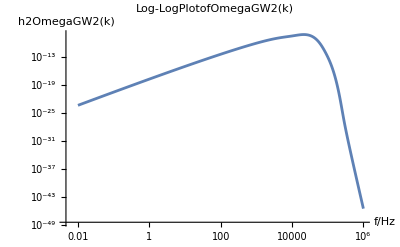

Key observation: This is the end of the GW integration script.